## General functions

```mathematica
user="Francisco Berkemeier";
(*user="franc";*)
<<MaTeX`
tickFunc=MapAt[Reverse,{All,3}]@*Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.01,.005}];
cellnl={"HeLa-S3","BJ1","IMR90","HUVEC","HCT","H1","H9","yeast"};
cellnnl={"HeLa","BJ","IMR90","HUVEC","HCT","H1","H9","S. cerevisiae"};
cela=AssociationThread[cellnl,cellnnl];
color=RGBColor[0.,0.43,0.65];
ft=FontFamily->"Bitstream Vera Sans";
st[s_]:=Style[s,FontFamily->"Bitstream Vera Sans",Black,12]
st2[s_]:=Style[s,FontFamily->"Bitstream Vera Sans",Black,10]
slabel=12;
saxes=16;
sbase=12;
ims=600;
dl=0.85;
dl2=0.78;

warmColors={RGBColor[0.5490196078431373,0.33725490196078434,0.29411764705882354] (*Brown*),RGBColor[0.8392156862745098,0.15294117647058825,0.1568627450980392],(*Red*)RGBColor[1.,0.4980392156862745,0.],(*Orange*)RGBColor[1.,0.8431372549019608,0.](*Gold/Yellow*)};
coldColors={RGBColor[0.12156862745098039,0.4666666666666667,0.7058823529411765],(*Blue*)RGBColor[0.,0.807843137254902,0.8196078431372549](*Teal/Cyan*),
RGBColor[0.75,0.96,0.96]};
allcolors=Join[warmColors,coldColors];
coloras=AssociationThread[cellnl[[1;;-2]],allcolors];
```

```mathematica
$RecursionLimit=1000;
```

```mathematica
ResourceFunction["MaTeXInstall"][];
ConfigureMaTeX[
"pdfLaTeX"->"C:\\Users\\"<>user<>"\\AppData\\Local\\Programs\\MiKTeX\\miktex\\bin\\x64\\pdflatex.exe",
"Ghostscript"->"C:\\Program Files\\gs\\gs10.01.2\\bin\\gswin64c.exe"
];
<<MaTeX`
```

## Figure fit convergence

```mathematica
RTf=Function[{n,f,v},
(1/f)(Sum[(E^(-f k^2/v)-E^(-f(k+1)^2/v))/(2k+1),{k,0,Ceiling[(n-3)/2]}]+E^(-f(Ceiling[(n-1)/2]^2)/v)/n)
];
```

```mathematica
sn=Graphics[{
Raster[Table[Blend[{RGBColor[{123,1,4}/255],RGBColor[{218,45,2}/255],RGBColor[{255,209,32}/255]},i],{j,1,100},{i,0,1,0.01}],{{0,0},{5,.5}},ColorFunction->Identity],
Blue,Rectangle[{5,0.},{5.1,.5}],
Black,Text[Style[MaTeX["1",FontSize->14],11,TextAlignment->Left],{0.,-0.5}],Text[Style[MaTeX["\\infty",FontSize->14],14,TextAlignment->Left],{5,-0.45}],Text[Style[MaTeX["n",FontSize->17],13],{2.5,-.5}]},ImageSize->Tiny]
```

-Graphics-

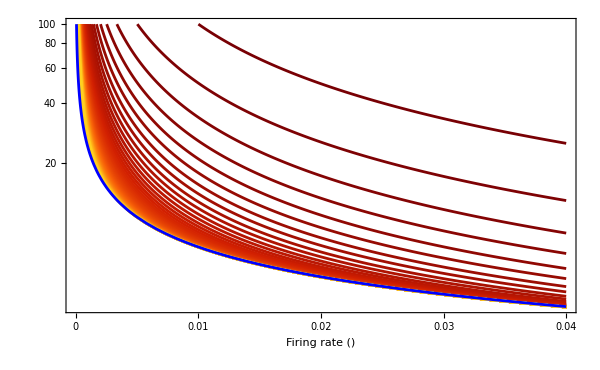

```mathematica
v=1.4;
Quiet@Show[
pl=ListLinePlot[Table[Table[{f,RTf[n,f,1.4]},{f,0.0001,0.04,0.0001}],{n,1,60}],PlotRange->{All,100},ScalingFunctions->{Automatic,"Log"},Frame->True,PlotStyle->"SolarColors",Epilog->Inset[sn,{.035,4.32}],ImageSize->ims,FrameLabel->{Style[Row[{"Firing rate (",MaTeX["f",FontSize->.9saxes+4],")"}],FontFamily->"Bitstream Vera Sans",.9saxes],Style[MaTeX["E[T;n]",FontSize->.9saxes+4],FontFamily->"Bitstream Vera Sans",Black,saxes]},

PlotRangePadding->0,
FrameTicks->{{tickFunc[##]&,None},{tickFunc[##]&,None}},

Axes->True,AxesOrigin->{0,0},PlotRange->All,Frame->True,PlotStyle->{RGBColor[0.267004,0.004874,0.329415],RGBColor[0.127568,0.566949,0.550556],RGBColor[0.993248,0.906157,0.143936]},ImageSize->Large,LabelStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->slabel}

],

(*Plot[
Sqrt[Log[2]/(v f)],{f,0.00005,0.04}
,PlotRange->{All,100},ScalingFunctions->{Automatic,"Log"},Frame->True,PlotStyle->Green,FrameLabel->{Style["Firing rate (f)",Black,FontFamily->"Bitstream Vera Sans"],"E[T;n]"},PlotLegends->Placed[{MaTeX["E[T;\\infty]\\simeq\\frac{1}{2}\\sqrt{\\frac{\\pi}{fv}}",FontSize->saxes]},{.17,.085}]],*)

Plot[
0.5Sqrt[Pi/(v f)],{f,0.00005,0.04}
,PlotRange->{All,100},ScalingFunctions->{Automatic,"Log"},Frame->True,PlotStyle->Blue,FrameLabel->{Style["Firing rate (f)",Black,FontFamily->"Bitstream Vera Sans"],"E[T;n]"},PlotLegends->Placed[{MaTeX["E[T;\\infty]\\simeq\\frac{1}{2}\\sqrt{\\frac{\\pi}{fv}}",FontSize->saxes]},{.17,.085}]]


]//Quiet
```

```mathematica
sn=Graphics[{
Raster[Table[Blend[{RGBColor[{123,1,4}/255],RGBColor[{218,45,2}/255],RGBColor[{255,209,32}/255]},i],{j,1,100},{i,0,1,0.01}],{{0,0},{5,.5}},ColorFunction->Identity],
Blue,Rectangle[{5,0.},{5.1,.5}],
Black,Text[Style[MaTeX["1",FontSize->14],11,TextAlignment->Left],{0.,-0.5}],Text[Style[MaTeX["\\infty",FontSize->14],14,TextAlignment->Left],{5,-0.45}],Text[Style[MaTeX["n",FontSize->17],13],{2.5,-.5}]},ImageSize->Tiny]
```

```mathematica
v=1.4;
Quiet@Show[
pl=ListLinePlot[Table[Table[{f,RTf[n,f,1.4]},{f,0.000001,0.00021,0.000001}],{n,0,600}],PlotRange->{50,500},ScalingFunctions->{Automatic,"Log"},Frame->True,PlotStyle->"SolarColors",Epilog->Inset[sn,{.035,4.32}],ImageSize->ims,FrameLabel->{Style[Row[{"Firing rate (",MaTeX["f",FontSize->.9saxes+4],")"}],FontFamily->"Bitstream Vera Sans",.9saxes],Style[MaTeX["E[T;n]",FontSize->.9saxes+4],FontFamily->"Bitstream Vera Sans",Black,saxes]},

PlotRangePadding->0,
FrameTicks->{{tickFunc[##]&,None},{tickFunc[##]&,None}},

Axes->True,AxesOrigin->{0,0},PlotRange->All,Frame->True,PlotStyle->{RGBColor[0.267004,0.004874,0.329415],RGBColor[0.127568,0.566949,0.550556],RGBColor[0.993248,0.906157,0.143936]},ImageSize->Large,LabelStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->slabel}

],

Plot[
Sqrt[Log[2]/(v f)],{f,0.000001,0.0004}
,PlotRange->{All,500},ScalingFunctions->{Automatic,"Log"},Frame->True,PlotStyle->Darker@Green,FrameLabel->{Style["Firing rate (f)",Black,FontFamily->"Bitstream Vera Sans"],"E[T;n]"},PlotLegends->Placed[{MaTeX["t_{\\text{rep}}=\\sqrt{\\frac{\\log(2)}{fv}}",FontSize->saxes]},{.15,.25}]],

Plot[
0.5Sqrt[Pi/(v f)],{f,0.0000001,0.0004}
,PlotRange->{All,500},ScalingFunctions->{Automatic,"Log"},Frame->True,PlotStyle->Blue,FrameLabel->{Style["Firing rate (f)",Black,FontFamily->"Bitstream Vera Sans"],"E[T;n]"},PlotLegends->Placed[{MaTeX["E[T;\\infty]\\simeq\\frac{1}{2}\\sqrt{\\frac{\\pi}{fv}}",FontSize->saxes]},{.17,.085}]]


]//Quiet
```

## Figure examples of periodic vs non-periodic

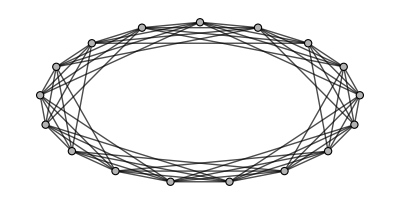

```mathematica
CirculantGraph[17,{1,2,3,4},AspectRatio->1/2,EdgeStyle->Black,VertexStyle->{_:>{GrayLevel[.7],EdgeForm[{Black}]} }]
```

```mathematica
fnper=Function[nMax,
solutions={};
For[m=1,m<=nMax,m++,For[l=0,l<=nMax-1,l++,n=(m-1)*l+m;
If[1<=n<=nMax,AppendTo[solutions,{n,m,l}];];];];
solutions];
fper=Function[nMax,
solutions={};
For[m=0,m<=nMax,m++,For[l=0,l<=nMax,l++,n=m*(l+1);
If[n>=1&&n<=nMax,AppendTo[solutions,{n,m,l}];];];];
Length@solutions];
```

```mathematica
fnper[4]
```

{{1,1,0},{1,1,1},{1,1,2},{1,1,3},{2,2,0},{3,2,1},{4,2,2},{3,3,0},{4,4,0}}

$Aborted

$Aborted

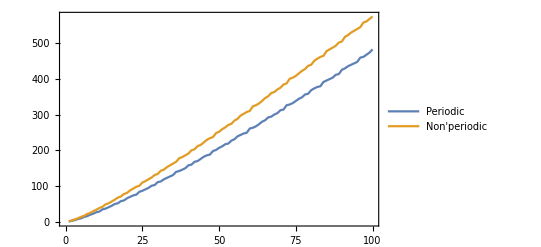

```mathematica
nmax=100;
fnperl=fnper/@Range[nmax];
fperl=fper/@Range[nmax];
ListLinePlot[{fperl,fnperl},Frame->True,PlotLegends->{"Periodic","Non'periodic"}]
```

## Figure fire rate histograms

```mathematica
dataall={};
data0={};
celln={"HeLa-S3","BJ1","IMR90","HUVEC","HCT","H1","H9"}[[7]];
Do[
Do[
AppendTo[dataall,Import["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Whole-Genome\\"<>j<>"\\fit_["<>j<>"]chr["<>ToString[i]<>"]_Whole-Genome\\fitfunction.txt","Lines"]],
{i,22}];
dataall=Flatten[dataall];
AppendTo[data0,Select[Flatten[ToExpression[StringSplit[#,","]]&/@dataall],10^-6<#<0.001&]],
{j,{celln}}];
```

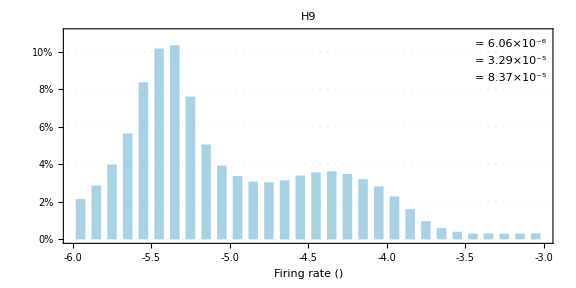

```mathematica
datap=data0[[1]];
f2[d_][{{xmin_,xmax_},{ymin_,ymax_}},___]:=Rectangle[{xmin+d (xmax-xmin)/2,ymin},{xmax-d (xmax-xmin)/2,ymax}]
mean=Mean[datap];
median=Median[datap];
std=StandardDeviation[datap];
tickFunc2=Module[{rawTicks},rawTicks=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.01,.005}][##];
rawTicks=MapAt[Reverse,rawTicks,{All,3}];
MapAt[PercentForm[#/. NumberForm[a_,___]:>PercentForm[Round[a,.01]]]&,rawTicks,{All,2}]]&;

Histogram[Log[10,datap],{.1},"Probability",GridLines->{None,Range[0,0.1,0.02]},Frame->True,
GridLinesStyle->Directive[Lighter[Gray,0.5],Dotted],
ChartStyle->Darker[RGBColor[{178,220,240}/255],0.05],ChartBaseStyle->EdgeForm[{None,Thickness[0],Opacity[1]}],
ChartElementFunction->f2[.4],
PlotRangeClipping->True,
PlotRangePadding->0,
FrameTicks->{{tickFunc2[##]&,None},{tickFunc[##]&,None}},
PlotRange->{0,.11},
dl0=0.81;
Epilog->{
Text[MaTeX["\\mu_{\\frac12}",FontSize->sbase+4],Scaled[{dl0-0.01,dl2+0.15}],Left,Background->White],
Text[StringForm["= ``",ScientificForm[N@median,3]],Scaled[{dl0+0.03,dl2+0.15}],Left,Background->White],
Text[MaTeX["\\mu",FontSize->sbase+4],Scaled[{dl0,dl2+0.07}],Left,Background->None],
Text[StringForm["= ``",ScientificForm[N@mean,3]],Scaled[{dl0+0.03,dl2+0.07}],Left,Background->None],
Text[MaTeX["\\sigma",FontSize->sbase+4],Scaled[{dl0,dl2-0.01}],Left,Background->None],
Text[StringForm["= ``",ScientificForm[N@std,3]],Scaled[{dl0+0.03,dl2-0.01}],Left,Background->White]},
FrameStyle->Black,
(*PlotLabel->Style[celln,Black,FontFamily->"Bitstream Vera Sans"],*)
PlotLabel->cela[celln],
LabelStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->slabel},
BaseStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->sbase},
FrameLabel->(Style[#,Black,saxes]&/@{Row[{"Firing rate (",MaTeX["\\log f",FontSize->saxes+4],")"}]}) ,AspectRatio->1/2,ImageSize->Large]
```

```mathematica
data0={};
cellnl={"HeLa-S3","BJ1","IMR90","HUVEC","HCT","H1","H9"};
Do[
dataall={};
Do[
AppendTo[dataall,Import["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Whole-Genome\\"<>j<>"\\fit_["<>j<>"]chr["<>ToString[i]<>"]_Whole-Genome\\fitfunction.txt","Lines"]],
{i,22}];
dataall=Flatten[dataall];
AppendTo[data0,Select[Flatten[ToExpression[StringSplit[#,","]]&/@dataall],10^-6<#<0.001&]],
{j,cellnl}];
```

```mathematica
warmColors={RGBColor[0.5490196078431373,0.33725490196078434,0.29411764705882354] (*Brown*),RGBColor[0.8392156862745098,0.15294117647058825,0.1568627450980392],(*Red*)RGBColor[1.,0.4980392156862745,0.],(*Orange*)RGBColor[1.,0.8431372549019608,0.](*Gold/Yellow*)};
coldColors={RGBColor[0.12156862745098039,0.4666666666666667,0.7058823529411765],(*Blue*)RGBColor[0.,0.807843137254902,0.8196078431372549](*Teal/Cyan*),
RGBColor[0.75,0.96,0.96]};
colors=Join[warmColors,coldColors];
```

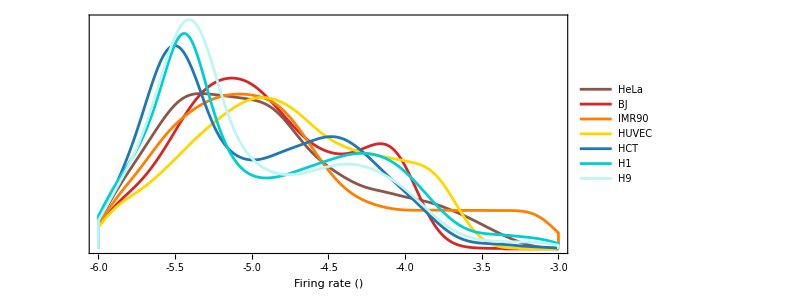

```mathematica
SmoothHistogram[Log[10,#]&/@(data0),.1,PlotRange->{{-6,-3},{0,All}},Frame->True,
PlotStyle->colors,
PlotLegends->Placed[Table[Style[i,Black,12,FontFamily->"Bitstream Vera Sans"],{i,cellnnl}],{0.9,0.67}],
PlotRangePadding->{0,0.02},
FrameTicks->{{None,None},{tickFunc[##]&,None}},
FrameStyle->Black,
BaseStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->sbase},FrameLabel->(Style[#,Black,saxes]&/@{Row[{"Firing rate (",MaTeX["\\log f",FontSize->saxes+4],")"}]}),AspectRatio->1/2,ImageSize->ims]
```

## Figure plot of time_real vs time_sim

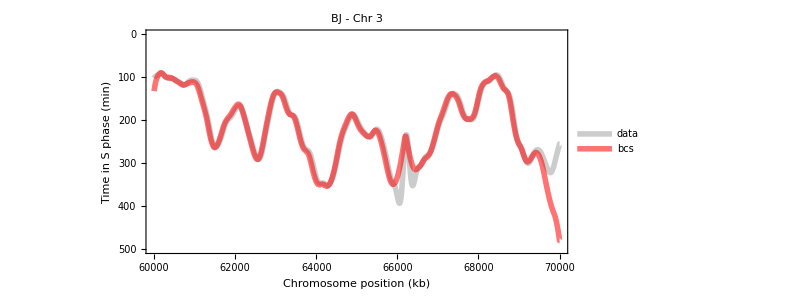

```mathematica
cell="BJ1";
chr=3;
minp=60000;
maxp=70000;
(*ext="_classic";*)
ext="";
st[s_]:=Style[s,FontFamily->"Bitstream Vera Sans",Black,14]
timereal=Import["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Large_fit\\"<>cell<>"\\fit_["<>cell<>"]chr["<>ToString@chr<>"]_"<>ToString@minp<>"-"<>ToString@maxp<>ext<>"\\time_real.txt","Lines"];
timereal=Flatten[ToExpression[StringSplit[#,","]]&/@timereal];
timesim=Import["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Large_fit\\"<>cell<>"\\fit_["<>cell<>"]chr["<>ToString@chr<>"]_"<>ToString@minp<>"-"<>ToString@maxp<>ext<>"\\time_sim.txt","Lines"];
timesim=Flatten[ToExpression[StringSplit[#,","]]&/@timesim];
AppendTo[timereal,timereal[[-1]]];
AppendTo[timesim,timesim[[-1]]];

ListLinePlot[{Transpose[{Range[minp,maxp],timereal}],Transpose[{Range[minp,maxp],timesim}]},
Frame->True,ImageSize->ims,PlotRange->{0,500},
AspectRatio->1/2,
PlotStyle->{{Opacity[.4,Gray],AbsoluteThickness[4]},{Opacity[.55,Red],AbsoluteThickness[4]}},
PlotLegends->Placed[LineLegend[{st@" data",st@" bcs"},Spacings->{0,-0.8},LegendMarkerSize->30],{.91,.89}],
PlotRangePadding->0,ImagePadding->{{60,30},{All,All}},
FrameTicks->{{tickFunc[##]&,None},{tickFunc[##]&,None}},ScalingFunctions->{Automatic,"Reverse"},
BaseStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->sbase},
LabelStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->slabel},
PlotLabel->cela[cell]<>" - Chr "<>ToString[chr],
FrameStyle->Black,
FrameLabel->(Style[#,Black,saxes]&/@{"Chromosome position (kb)",Style[Row[{"Time in S phase (min)"}],FontFamily->"Bitstream Vera Sans",16]})

(*,Epilog->{
Text[MaTeX["v=0.28\\text{ kb/min}",FontSize->sbase+4],Scaled[{0.5,0.1}],Center,Background->White]}*)
]
```

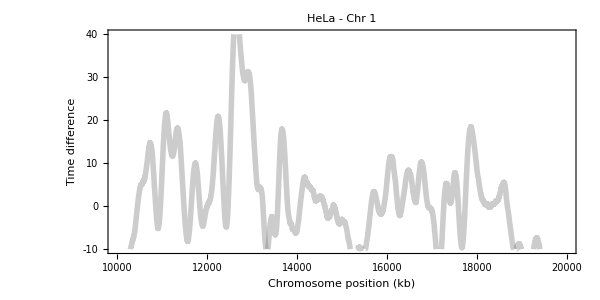

```mathematica
cell="HeLa-S3";
chr=1;
minp=10000;
maxp=20000;
(*ext="_classic";*)
ext="";
st[s_]:=Style[s,FontFamily->"Bitstream Vera Sans",Black,14]
timereal=Import["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Large_fit\\"<>cell<>"\\fit_["<>cell<>"]chr["<>ToString@chr<>"]_"<>ToString@minp<>"-"<>ToString@maxp<>ext<>"\\time_real.txt","Lines"];
timereal=Flatten[ToExpression[StringSplit[#,","]]&/@timereal];
timesim=Import["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Large_fit\\"<>cell<>"\\fit_["<>cell<>"]chr["<>ToString@chr<>"]_"<>ToString@minp<>"-"<>ToString@maxp<>ext<>"\\time_sim.txt","Lines"];
timesim=Flatten[ToExpression[StringSplit[#,","]]&/@timesim];
AppendTo[timereal,timereal[[-1]]];
AppendTo[timesim,timesim[[-1]]];

ListLinePlot[{Transpose[{Range[minp,maxp],timereal-timesim}]},
Frame->True,ImageSize->ims,PlotRange->{-10,40},
AspectRatio->1/2,
PlotStyle->{{Opacity[.4,Gray],AbsoluteThickness[4]},{Opacity[.55,Red],AbsoluteThickness[4]}},
(*PlotLegends->Placed[LineLegend[{st@" data",st@" bcs"},Spacings->{0,-0.8},LegendMarkerSize->30],{.91,.89}],*)
PlotRangePadding->0,ImagePadding->{{60,30},{All,All}},
FrameTicks->{{tickFunc[##]&,None},{tickFunc[##]&,None}},ScalingFunctions->{Automatic,Automatic},
BaseStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->sbase},
LabelStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->slabel},
PlotLabel->cela[cell]<>" - Chr "<>ToString[chr],
FrameStyle->Black,
FrameLabel->(Style[#,Black,saxes]&/@{"Chromosome position (kb)",Style[Row[{"Time difference"}],FontFamily->"Bitstream Vera Sans",16]})

(*,Epilog->{
Text[MaTeX["v=0.28\\text{ kb/min}",FontSize->sbase+4],Scaled[{0.5,0.1}],Center,Background->White]}*)
]
```

## Figure plot of time_real vs time_sim (general files)

#### General file generation

```mathematica
cell="BJ1";
chr=3;

(*Function to handle file import or zero string generation*)
importOrZeroes[file_]:=Module[{exists,zeroString},exists=FileExistsQ[file];
If[exists,Import[file,"Text"],zeroString=StringJoin[Riffle[Table["0",{10000}],"\n"]];
zeroString]];

(*Read the contents of the files or generate zero strings*)
filelreal=Table[importOrZeroes["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Large_fit\\"<>cell<>"\\fit_["<>cell<>"]chr["<>ToString@chr<>"]_"<>ToString@(10000*j)<>"-"<>ToString@(10000*(j+1))<>"\\time_real.txt"],{j,0,23}];
filelsim=Table[importOrZeroes["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Large_fit\\"<>cell<>"\\fit_["<>cell<>"]chr["<>ToString@chr<>"]_"<>ToString@(10000*j)<>"-"<>ToString@(10000*(j+1))<>"\\time_sim.txt"],{j,0,23}];

(*Join the contents*)
filereal=StringJoin[Riffle[filelreal,"\n"]];
filesim=StringJoin[Riffle[filelsim,"\n"]];

(*Export the joined contents to a new file*)
Export["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Large_fit\\"<>cell<>"\\fit_["<>cell<>"]chr["<>ToString@chr<>"]_All\\time_real_all.txt",filereal];
Export["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Large_fit\\"<>cell<>"\\fit_["<>cell<>"]chr["<>ToString@chr<>"]_All\\time_sim_all.txt",filesim];
```

#### Previous plots (general file version)

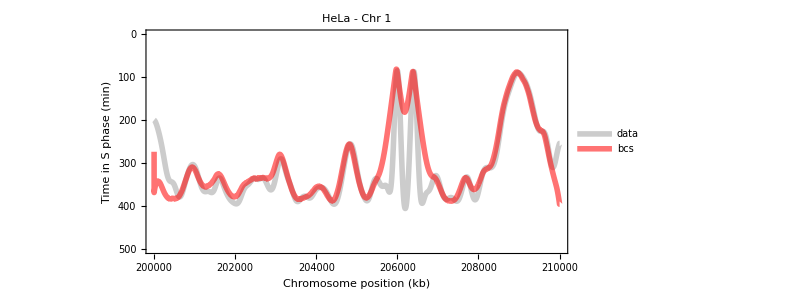

```mathematica
cell="HeLa-S3";
chr=1;
minp=200000;
maxp=210000;
(*ext="_classic";*)
ext="";
st[s_]:=Style[s,FontFamily->"Bitstream Vera Sans",Black,14]
timereal0=Import["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Large_fit\\"<>cell<>"\\fit_["<>cell<>"]chr["<>ToString@chr<>"]_All\\time_real_all.txt","Lines"][[minp;;maxp-1]];
timereal0=Flatten[ToExpression[StringSplit[#,","]]&/@timereal0];
timesim0=Import["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Large_fit\\"<>cell<>"\\fit_["<>cell<>"]chr["<>ToString@chr<>"]_All\\time_sim_all.txt","Lines"][[minp;;maxp-1]];
timesim0=Flatten[ToExpression[StringSplit[#,","]]&/@timesim0];
AppendTo[timereal0,timereal0[[-1]]];
AppendTo[timesim0,timesim0[[-1]]];

dplot=ListLinePlot[{Transpose[{Range[minp,maxp],timereal0}],Transpose[{Range[minp,maxp],timesim0}]},
Frame->True,ImageSize->ims,PlotRange->{0,500},
AspectRatio->1/2,
PlotStyle->{{Opacity[.4,Gray],AbsoluteThickness[4]},{Opacity[.55,Red],AbsoluteThickness[4]}},
PlotLegends->Placed[LineLegend[{st@" data",st@" bcs"},Spacings->{0,-0.8},LegendMarkerSize->30],{.91,.89}],
PlotRangePadding->0,ImagePadding->{{60,30},{All,All}},
FrameTicks->{{tickFunc[##]&,None},{tickFunc[##]&,None}},ScalingFunctions->{Automatic,"Reverse"},
BaseStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->sbase},
LabelStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->slabel},
PlotLabel->cela[cell]<>" - Chr "<>ToString[chr],
FrameStyle->Black,
FrameLabel->(Style[#,Black,saxes]&/@{"Chromosome position (kb)",Style[Row[{"Time in S phase (min)"}],FontFamily->"Bitstream Vera Sans",16]})

(*,Epilog->{
Text[MaTeX["v=0.28\\text{ kb/min}",FontSize->sbase+4],Scaled[{0.5,0.1}],Center,Background->White]}*)
]
```

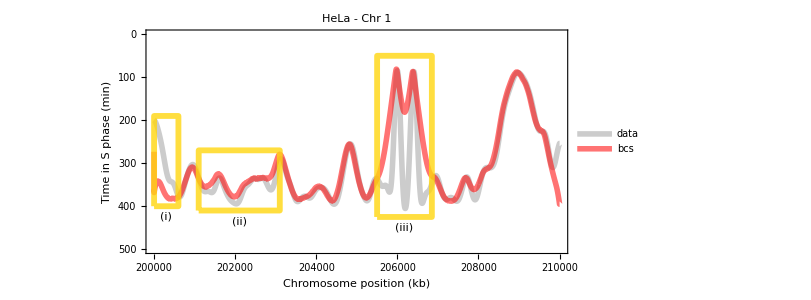

```mathematica
br1={206850,-425}; 
tr1={205500,-50};     
rec1=Graphics[{EdgeForm[{RGBColor[1.,0.84,0.06],Thickness[.007],Opacity[.8]}],FaceForm[None],Rectangle[br1,tr1]}];
text1=Graphics[Style[Text["(iii)",{206175,-450}],ft,Bold]];
br2={200000,-190}; 
tr2={200600,-400};     
rec2=Graphics[{EdgeForm[{RGBColor[1.,0.84,0.06],Thickness[.007],Opacity[.8]}],FaceForm[None],Rectangle[br2,tr2]}];
text2=Graphics[Style[Text["(i)",{200300,-425}],ft,Bold]];
br3={201100,-270}; 
tr3={203100,-410};     
rec3=Graphics[{EdgeForm[{RGBColor[1.,0.84,0.06],Thickness[.007],Opacity[.8]}],FaceForm[None],Rectangle[br3,tr3]}];
text3=Graphics[Style[Text["(ii)",{202100,-435}],ft,Bold]];

(*Overlay the rectangle on the existing plot*)
Show[dplot,rec1,rec2,rec3,text1,text2,text3]
```

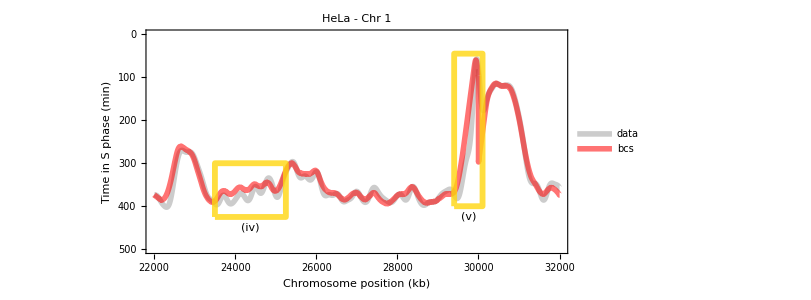

```mathematica
br1={25250,-425}; 
tr1={23500,-300};     
rec1=Graphics[{EdgeForm[{RGBColor[1.,0.84,0.06],Thickness[.007],Opacity[.8]}],FaceForm[None],Rectangle[br1,tr1]}];
text1=Graphics[Style[Text["(iv)",{Mean[{br1[[1]],tr1[[1]]}],-450}],ft,Bold]];
br2={29400,-45}; 
tr2={30100,-400};     
rec2=Graphics[{EdgeForm[{RGBColor[1.,0.84,0.06],Thickness[.007],Opacity[.8]}],FaceForm[None],Rectangle[br2,tr2]}];
text2=Graphics[Style[Text["(v)",{Mean[{br2[[1]],tr2[[1]]}],-425}],ft,Bold]];

(*Overlay the rectangle on the existing plot*)
Show[dplot,rec1,rec2,text1,text2]
```

#### Components

```mathematica
(* Cell and chromosome details *)
cell="HeLa-S3";
chr=1;
ext="";
st[s_]:=Style[s,FontFamily->"Bitstream Vera Sans",Black,14]
timereal=Import["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Large_fit\\"<>cell<>"\\fit_["<>cell<>"]chr["<>ToString@chr<>"]_All\\time_real_all.txt","Lines"];
timereal=Flatten[ToExpression[StringSplit[#,","]]&/@timereal];
timesim=Import["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Large_fit\\"<>cell<>"\\fit_["<>cell<>"]chr["<>ToString@chr<>"]_All\\time_sim_all.txt","Lines"];
timesim=Flatten[ToExpression[StringSplit[#,","]]&/@timesim];
AppendTo[timereal,timereal[[-1]]];
AppendTo[timesim,timesim[[-1]]];
errtime=timesim-timereal;
errtimea=Abs[errtime];
percentageLess[list_,number_]:=Count[list,x_/;x>number]/Length[list];

number=10;
nmin=1;
errtimeapos=Position[errtimea,x_/;x<nmin||x>number];
```

```mathematica
(* CENTROMERES *)
cmeres={125000,93300,91000,50400,48400,61000,59900,45600,49000,40200,53700,35800,17900,17600,19000,36600,24000,17200,26500,27500,13200,14700};
cmeresl={7400,6300,6000};

(*Function to count occurrences based on condition in both directions*)
countCentromere[list_,positions_,num_]:=Module[{countLeft,countRight,total,startPos},
countLeft[pos_]:=LengthWhile[Reverse[list[[;;pos]]],#<1||#>num&];
countRight[pos_]:=LengthWhile[list[[pos;;]],#<1||#>num&];
Table[startPos=positions[[i]];
cleft=countLeft[startPos];
cright=countRight[startPos+1];
total=cleft+cright-1;
{startPos,total+1,startPos-cleft,startPos+cright},{i,1,Length[positions]}]];

occurrences=countCentromere[errtimea,{cmeres[[chr]]},number];

positcmeres=Flatten[Map[Range[#[[1]],#[[2]]]&,occurrences[[All,{3,4}]]]];
countcmeres=Total[occurrences[[All,2]]];
percecmeres=countcmeres/Length[errtimeapos]//N
```

0.235671

```mathematica
(* TELOMERES *)
tmeres={1,Length[errtimea]};
tmeresl={7400,6300,6000};

(*Function to count occurrences based on condition in both directions*)
countCentromere[list_,positions_,num_]:=Module[{countLeft,countRight,total,startPos},
countLeft[pos_]:=LengthWhile[Reverse[list[[;;pos]]],#<1||#>num&];
countRight[pos_]:=LengthWhile[list[[pos;;]],#<1||#>num&];
Table[startPos=positions[[i]];
cleft=countLeft[startPos];
cright=countRight[startPos+1];
total=cleft+cright-1;
{startPos,total+1,startPos-cleft,startPos+cright},{i,1,Length[positions]}]];

occurrences=countCentromere[errtimea,tmeres,number]

posittmeres=Flatten[Map[Range[#[[1]],#[[2]]]&,occurrences[[All,{3,4}]]]];
counttmeres=Total[occurrences[[All,2]]];
percetmeres=counttmeres/Length[errtimeapos]//N
```

{{1,10300,0,10300},{240001,184,239817,240001}}

0.0861257

```mathematica
(* SIMULATION BOUNDS *)
sbound=Table[10000*j,{j,2,21}];
(*Function to count occurrences based on condition in both directions*)
countOccurrences[list_,positions_,num_]:=Module[{countLeft,countRight,total,startPos},
countLeft[pos_]:=LengthWhile[Reverse[list[[;;pos]]],#>num&];
countRight[pos_]:=LengthWhile[list[[pos;;]],#>num&];
Table[startPos=positions[[i]];
cleft=countLeft[startPos];
cright=countRight[startPos+1];
total=cleft+cright-1;
{startPos,total+1,startPos-cleft,startPos+cright},{i,1,Length[positions]}]];

(*Calculate occurrences*)
occurrences=countOccurrences[errtimea,sbound,number];

positsbound=Complement[Flatten[Map[Range[#[[1]],#[[2]]]&,occurrences[[All,{3,4}]]]],Join[{posittmeres,positcmeres}]];
countsbound=Length[positsbound];
percesbound=countsbound/Length[errtimeapos]//N;
```

```mathematica
errtime[[1]]
```

0

```mathematica
(* FORK STALLING *)
positfstall=Complement[Flatten[Position[errtime,_?(#<0&&Abs[#]>number&)]],Join[{posittmeres,positcmeres}]];
countfstall=Length[positfstall];
percefstall=countfstall/Length[errtimeapos]//N;
```

```mathematica
(* TOTAL RESULTS *)
percesl={percesbound,percecmeres,percetmeres,percefstall};
perceother=1-Total[percesl];
percentages=Append[percesl,perceother];
```

#### Components function

```mathematica
compf=Function[{cell,chr,number},
(* Cell and chromosome details *)
st[s_]:=Style[s,FontFamily->"Bitstream Vera Sans",Black,14];
timereal=Import["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Large_fit\\"<>cell<>"\\fit_["<>cell<>"]chr["<>ToString@chr<>"]_All\\time_real_all.txt","Lines"];
timereal=Flatten[ToExpression[StringSplit[#,","]]&/@timereal];
timesim=Import["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Large_fit\\"<>cell<>"\\fit_["<>cell<>"]chr["<>ToString@chr<>"]_All\\time_sim_all.txt","Lines"];
timesim=Flatten[ToExpression[StringSplit[#,","]]&/@timesim];
AppendTo[timereal,timereal[[-1]]];
AppendTo[timesim,timesim[[-1]]];
errtime=timesim-timereal;
errtimea=Abs[errtime];

errtimeapos=Flatten[Position[errtimea,x_/;x<1||x>number||N@x==0.]];


(* SIMULATION BOUNDS *)
sbound=Table[10000*j,{j,2,21}];
(*Function to count occurrences based on condition in both directions*)
countOccurrences[list_,positions_,num_,nmin_]:=Module[{countLeft,countRight,total,startPos},
countLeft[pos_]:=LengthWhile[Reverse[list[[;;pos]]],#<nmin||#>num&];
countRight[pos_]:=LengthWhile[list[[pos;;]],#<nmin||#>num&];
Table[startPos=positions[[i]];
cleft=countLeft[startPos];
cright=countRight[startPos+1];
total=cleft+cright-1;
{startPos,total+1,startPos-cleft,startPos+cright},{i,1,Length[positions]}]];
(*Calculate occurrences*)
occurrences=countOccurrences[errtimea,sbound,number,-1];

positsbound0=Intersection[errtimeapos,Flatten[Map[Range[#[[1]],#[[2]]]&,occurrences[[All,{3,4}]]]]];
positsbound=positsbound0;
countsbound=Length[positsbound];
percesbound=countsbound/Length[errtimeapos]//N;


(* CENTROMERES *)
cmeres={130000,93300,91000,50400,48400,61000,59900,45600,49000,40200,53700,35800,17900,17600,19000,36600,24000,17200,26500,27500,13200,14700};
cmeresl={7400,6300,6000};
occurrences=countOccurrences[errtimea,{cmeres[[chr]]},number,1];

positcmeres0=Intersection[errtimeapos,Flatten[Map[Range[#[[1]],#[[2]]]&,occurrences[[All,{3,4}]]]]];
positcmeres=DeleteElements[positcmeres0,positsbound];
countcmeres=Total[occurrences[[All,2]]];
percecmeres=countcmeres/Length[errtimeapos]//N;


(* TELOMERES *)
tmeres={1,Length[errtimea]};
tmeresl={7400,6300,6000};
occurrences=countOccurrences[errtimea,tmeres,number,1];

posittmeres0=Intersection[errtimeapos,Flatten[Map[Range[#[[1]],#[[2]]]&,occurrences[[All,{3,4}]]]]];
posittmeres=DeleteElements[posittmeres0,positsbound];
counttmeres=Total[occurrences[[All,2]]];
percetmeres=counttmeres/Length[errtimeapos]//N;


(* FORK STALLING *)
positfstall0=Intersection[errtimeapos,Flatten[Position[errtime,_?(#>0&&Abs[#]>number&)]]];
positfstall=DeleteElements[positfstall0,positsbound];
countfstall=Length[positfstall];
percefstall=countfstall/Length[errtimeapos]//N;


(* FRAGILE SITES *)
excelFilePath="C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\FragileSites\\fragilesites.xlsx";
sheetName="Sheet1";
data=Import[excelFilePath,{"Sheets",sheetName}];
chrColumn=Position[data[[1]],"chr"<>ToString[chr]][[1,1]];
values=data[[2;;,chrColumn]];
pairsList=ToExpression/@(StringSplit[#,"-"]&/@values);
divideKeepingOne[x_]:=If[x==1,1,Floor[x/1000.]];
scaledList=Map[divideKeepingOne,pairsList,{2}];

positfrag0=Intersection[errtimeapos,Flatten[Range@@@scaledList]];
positfrag=DeleteElements[positfrag0,positsbound];
countfrag=Length[positfrag];
percefrag=countfrag/Length[errtimeapos]//N;


(* OTHER *)
combinedPositions=Union[positcmeres,positfrag,positfstall,positsbound,posittmeres];
positother=Complement[errtimeapos,combinedPositions];
countother=Length[positother];
perceother=countother/Length[errtimeapos]//N;


(* ALL *)
percesl={percesbound,percecmeres,percetmeres,percefstall,percefrag,perceother};


(* TOTAL RESULTS *)
{percesl,N@Count[errtimea,x_/;x<number]/Length[timereal]}];
```

#### Mock data

```mathematica
celllist={"HeLa-S3","BJ1","IMR90","HUVEC","HCT","H1","H9"};
bfun[x_]:=If[0<x<1,x,x-Sign[x]RandomReal[.01]]
percel=Abs@Table[bfun[#+RandomReal[{-0.1,0.1}]]&/@{0.09,0.23,0.09,0.11,0.56,0.14},{j,Length@celllist}];
compareNumbers={1,2,5,10,20};
class=cela/@celllist;
errorl=Transpose@Table[Sort[bfun[#+RandomReal[{-0.1,0.1}]]&/@{0.24,0.32,0.52,0.80,0.92}],{j,Length@class}];

compareNumbers=Range[20];
errorl=Transpose@Table[Sort[bfun[#+RandomReal[{-0.1,0.1}]]&/@{0.24,0.32,0.38,0.4,0.52,0.59,0.62,0.68,0.76,0.80,0.81,0.81,0.83,0.84,0.85,0.87,0.88,0.9,0.9,0.92}],{j,Length@class}];
```

#### Plots

```mathematica
arrayl={};
celllist0={"HeLa-S3","HCT","H1"};
Do[
compf[celllist0[[j]],1,10];
maxerr=100;
errtimea0=If[N@#<10.^(-1)||N@#>maxerr,maxerr,#]&/@errtimea;
ForestGreen=RGBColor[0.13,0.55,0.13];
customColorFunction[value_]:=Blend[{ForestGreen,Yellow,Red},value];
dataerr={errtimea0};
AppendTo[arrayl,{cela[celllist0[[j]]],ArrayPlot[dataerr,Frame->{{False,False},{j==Length@celllist0,False}},ColorFunction->customColorFunction,FrameTicks->{None,Automatic},AspectRatio->1/26,ImageSize->800,FrameLabel->{{"Chromosome position (kb)",None},{None,None}},PlotRangePadding->{0,{.5,0}}]}]
,{j,Length@celllist0}];
gridbars=Grid[arrayl,Spacings->{Automatic,-.3},Alignment->{Right,Top}]
(*Export["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Figures\\gridbars.pdf",gridbars];*)
```

```mathematica
maxerr=100;
errtimea0=If[N@#<10.^(-1)||N@#>maxerr,maxerr,#]&/@errtimea;
ForestGreen=RGBColor[0.13,0.55,0.13];
customColorFunction[value_]:=Blend[{ForestGreen,Yellow,Red},value];
dataerr={errtimea0};
ArrayPlot[dataerr,Frame->{{False,False},{True,False}},ColorFunction->customColorFunction,FrameTicks->{None,Automatic},AspectRatio->1/14,ImageSize->800]
```

```mathematica
celllist={"HeLa-S3","HCT","H1"};
percentages=compf[#,1,10]&/@celllist;
percel=percentages[[All,1]];
```

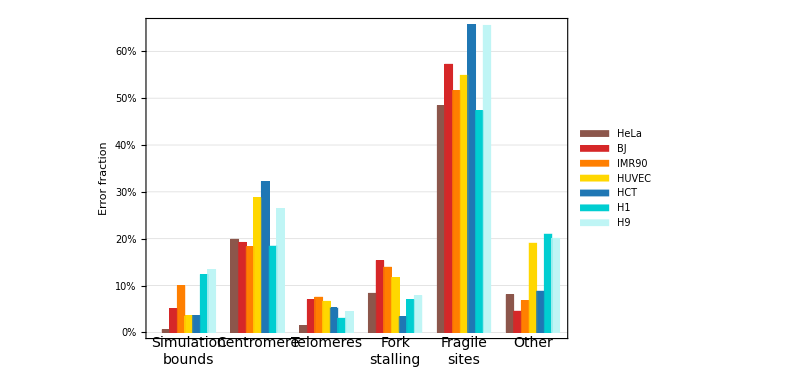

```mathematica
(*Categories*)categories=Style[#,14]&/@{"Simulation\nbounds","Centromere","Telomeres","Fork\nstalling","Fragile\nsites","Other"};
class=Style[#,14]&/@cela/@celllist;
(*Softer,warm colors for the bars in each triple*)
barColors=(coloras/@celllist);
(*Custom tick function for percentage format with 10% intervals*)
percentageTicks[low_,high_]:=Table[{i,Style[ToString[Round[i*100]]<>"%",13]},{i,low,high,0.1}];
(*Create the bar chart*)
barcharts=BarChart[Transpose@percel,ChartLabels->{Placed[categories,Below],None},ChartStyle->barColors,PlotTheme->"Detailed",BarSpacing->{None,2},AxesLabel->{"Category","Percentage"},LabelingFunction->None,ChartLegends->Placed[class,{0.09,0.78}],FrameTicks->{{percentageTicks,None},{None,None}},ScalingFunctions->{Automatic,Automatic},ImageSize->ims,FrameLabel->Style["Error fraction",15,Black]]
(*Export["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Figures\\barcharts.pdf",barcharts]*)
```

```mathematica
compf["HeLa-S3",1,10];
```

```mathematica
int123=Length@Intersection[positfrag,positfstall,posittmeres];
int124=Length@Intersection[positfrag,positfstall,positcmeres];
int13=Length@Intersection[positfrag,posittmeres]-int123;
int14=Length@Intersection[positfrag,positcmeres]-int124;
int23=Length@Intersection[positfstall,posittmeres]-int123;
int24=Length@Intersection[positfstall,positcmeres]-int124;
int12=Length@Intersection[positfrag,positfstall]-(int123+int124);
int1=Length[positfrag]-(int123+int124+int12+int13+int14);
int2=Length[positfstall]-(int123+int124+int12+int23+int24);
int3=Length[posittmeres]-(int123+int13+int23);
int4=Length[positcmeres]-(int124+int23+int24);

setlist0={int1,int2,int3,int4,int12,int13,int14,int23,int24,int123,int124};
setlist0=N@setlist0/Total[setlist0];
setlist=ToString[Round[#*100,0.1]]<>"%"&/@setlist0;
setlist={"29.5%","7.1%","0.1%","28.9%","5.8%","9.6%","20.3%","0.2%","0.1%","0.3%","0.1%"};
```

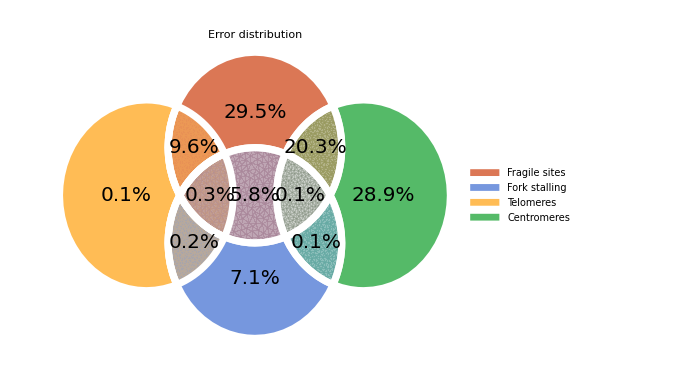

```mathematica
a=Disk[{0,0.5}];
b=Disk[{0,-0.5}];
c=Disk[{1.25,0}];
d=Disk[{-1.25,0}];

subsets=Subsets[{a,b,d,c},{1,4}];
subsetscolors=Lighter@Map[Function[{c},Blend[Flatten[Map[Table[Map[Append[#,1.5/Length[c]]&,c],3]&,c]]]],Subsets[Map[ColorData[112],Range[4]],{1,5}]];

positionList={{0,0.87},{0,-0.87},{-1.48,0},{1.48,0},{0,0},{-0.7,0.5},{0.7,0.5},{-0.7,-0.5},{0.7,-0.5},{-0.52,0},{0.52,0}};
epilog=Table[Text[Style[setlist[[j]],Black,20],positionList[[j]]],{j,11}];

venndig=RegionPlot[Evaluate[DiscretizeRegion[RegionDifference[BooleanRegion[And,#],BooleanRegion[Or,Complement[{a,b,c,EmptyRegion[2]},#]]]]&/@subsets],Sequence[PlotStyle->subsetscolors,BoundaryStyle->Directive[Thickness[0.01],White],Frame->False,LabelStyle->{24},PerformanceGoal->"Speed",ImageSize->510],AspectRatio->0.73,Epilog->epilog,PlotLegends->Placed[Style[#,15,Black]&/@{"Fragile sites","Fork stalling","Telomeres","Centromeres"},Below],PlotLabel->Style["Error distribution",16,Black],PlotStyle->Opacity[0.3]]

(*Export["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Figures\\vendiag.pdf",venndig]*)
```

```mathematica
(*Define the numbers to compare against*)
compareNumbers={1,2,5,10,20};
errorl=Table[compf[#,1,j][[2]]&/@celllist,{j,compareNumbers}];
```

```mathematica
(*Invert the color scheme*)
invertedSunsetColors[x_]:=ColorData["SunsetColors"][1-x];

(*Create a grid of colored squares with labels*)
createColoredGrid[errorl_,compareNumbers_]:=Module[{grid,colLabels,legend,legendSize},(*Create the main grid with colored squares*)grid=Table[Graphics[{invertedSunsetColors[errorl[[k,j]]],Rectangle[]},ImageSize->{50,50}],{k,Length@compareNumbers},{j,Length@class}];
grid=MapThread[Prepend,{grid,compareNumbers}];
colLabels=Prepend["chr "<>ToString[#]&/@Range[Length[errorl]],""];
colLabels={,Sequence@@class};
grid=Prepend[grid,colLabels];
legendSize=50*Length[compareNumbers]-2;
legend=BarLegend[{invertedSunsetColors,{0,1}},LegendLayout->"Column",LegendMarkerSize->legendSize,LabelingFunction->(Row[{100*#,"%"}]&)];
Labeled[Grid[grid,Spacings->{0,0}],legend,Right,LabelStyle->Medium]];

(*Create and display the grid with labels and percentage bar*)
coloredGrid=createColoredGrid[errorl,compareNumbers];
coloredGrid
(*Export["C:\\Users\\Francisco Berkemeier\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Figures\\gridcolored.pdf",coloredGrid]*)
```

Part::partw: Part 2 of Sort[inilist] does not exist.

Part::partw: Part 3 of Sort[inilist] does not exist.

Part::partw: Part 4 of Sort[inilist] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*Invert the color scheme*)
invertedSunsetColors[x_]:=ColorData["SunsetColors"][1-x];

(*Create a grid of colored squares with labels*)
createColoredGrid[errorl_,compareNumbers_]:=Module[{grid,colLabels,legend,legendSize},(*Create the main grid with colored squares*)

meanerrorl=Mean/@errorl;
errorlm=Transpose[Append[meanerrorl]@Transpose[errorl]];

grid=Table[Graphics[{invertedSunsetColors[errorlm[[k,j]]],Rectangle[]},ImageSize->{40,40}],{k,Length@compareNumbers},{j,Length@(Append[class,"Mean"])}];

colLabels={Sequence@@Text/@st/@Append[class,"Mean"]};
grid=Prepend[grid,colLabels];
(*grid=MapThread[Append,{grid,Transpose@compareNumbers}];*)
(*grid=MapThread[Append,{grid,{ConstantArray["s",20]}}];*)
grid=Transpose[Append[Join[{Null},st/@Range[20]]]@Transpose[grid]];
grid=Transpose[Append[Join[{Null,Style[Row[{"Time threshold ",MaTeX["\\tau",FontSize->22]," (min)"}],18,ft]},ConstantArray[SpanFromLeft,19]]]@Transpose[grid]];
grido=grid;

legendSize=15*Length[compareNumbers];
legend=BarLegend[{invertedSunsetColors,{0,1}},LegendLayout->"Column",LegendMarkerSize->legendSize,LabelingFunction->(Row[st2/@{Floor[100*#],"%"}]&)];
Labeled[Grid[Transpose@grid,Spacings->{Join[{All,.5},ConstantArray[-.15,Length[errorlm]]],Join[ConstantArray[-.45,7],{.5,.5,.8}]},Alignment->{Center,Automatic,{{{1,-1},{1,1}}->Right}},
ItemSize->Full
],legend,{{Right,Top}},LabelStyle->Medium]];

(*Create and display the grid with labels and percentage bar*)
coloredGrid=createColoredGrid[errorlm,compareNumbers]
axis=Graphics[AxisObject[{"Horizontal",0},AxisLabel->Placed["Time (min)",Center]],PlotRange->{{0,20},{0,18}}];
(*Export["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Figures\\gridcolored.pdf",coloredGrid]*)
```

HeLa | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
BJ | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
IMR90 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HUVEC | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HCT | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
H1 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
H9 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Mean | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
 | Time threshold -Graphics- (min) |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
CalculateFraction[replicationTimes_List,t_]:=Module[{lessThanT},lessThanT=N@Count[replicationTimes,x_/;x<t];
lessThanT/Length[replicationTimes]]
```

```mathematica
compareNumbers=Range[0,20,.1];
inilist=CalculateFraction[errtimea,#]&/@compareNumbers;
errorl=Transpose@Table[Sort[Abs@bfun[#+RandomReal[{-0.1,0.1}]]&/@inilist],{j,Length@class}];
```

```mathematica
ClearAll[preProcessData,preProcessData2,circularLegend,labelingFunction]

preProcessData[data_,gap_:Automatic,clr_:"SunsetColors"]:=Module[{del=gap/. Automatic->1/16,slices=ConstantArray[1/#[[2]],#]&@Dimensions[data]},Append[del->{Null,0}]/@MapThread[Thread[#->Transpose[{##2}]]&,{Rescale[slices,{0,1},{0,1-del}],Rescale[data,{0,100}],data}]/. Rule[a_,{b1_,b2_}]:>Style[Labeled[{a,1},b2,Tooltip],
ColorData[clr]@(1-b1)]]
preProcessData2[data_,gap_:Automatic,clr_:"SunsetColors"]:=Module[{del=gap/. Automatic->1/16,slices=ConstantArray[1/#[[2]],#]&@Dimensions[data]},Append[del->{Null,0}]/@MapThread[Thread[#->Transpose[{##2}]]&,{Rescale[slices,{0,1},{0,1-del}],Rescale[data],data}]/. Rule[a_,{b1_,b2_}]:>Style[Labeled[{a,1},b2,Tooltip],
ColorData[clr]@(1-b1)]]

invcol[x_]:=ColorData["SunsetColors"][1-x];
circularLegend[min_,max_,colorscheme_:"SunsetColors"]:=AngularGauge[min,{min,max},ScaleOrigin->{{Pi/2,2 Pi},1.1},ScaleRanges->({#,.3}&/@Partition[Subdivide[min,max,50],2,1]),"TickSide"->Left,"LabelSide"->Left,"TickLength"->{Scaled[.04],Scaled[0.02]},TicksStyle->FontSize->Scaled[.07],GaugeMarkers->None,ScaleRangeStyle->invcol,GaugeFrameStyle->None]

labelingFunction[nrows_,collabels_]:=If[#2[[1]]==nrows,Placed[collabels[[#2[[2]]]],{1/2,1.1}]]&
```

```mathematica
data1=RandomReal[{60,100},{Length@class,22}];

columnlabels=Append[Style[ToString@#,14]&/@Range[Last@Dimensions[data1]],""];

rowlabels=Style[#,16]&/@class//Reverse;

radialorigin=4;

gap=1/16;

wheel1=SectorChart[preProcessData[data1],SectorOrigin->{{Pi/2+gap Pi,"Counterclockwise"},radialorigin},ChartBaseStyle->Directive[EdgeForm[{Opacity[1],White}]],LabelingFunction->labelingFunction[First@Dimensions@data1,columnlabels],ChartElementFunction->Append[ConstantArray["Sector",Length@First@data1],{}&],ChartLegends->Placed[circularLegend[0(*Min@data1*),100(*Max@data1*)],Center],ImageSize->700,SectorSpacing->{0,0},Epilog->{Text[Style["Genome\n(%)",Black,16],{0,0}],MapIndexed[Text[#,{0,radialorigin-1/2+#2[[1]]}]&,rowlabels]}]

(*Export["C:\\Users\\Francisco Berkemeier\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Figures\\wheel1mock.pdf",wheel1];*)
```

-Graphics-

```mathematica
data1=RandomReal[{5,10},{Length@class,22}];
data2=RandomReal[{5,15},{Length@class,22}];
data3=RandomReal[{55,65},{Length@class,22}];

data1=RandomVariate[SkewNormalDistribution[15,5,-0.1],{Length@class,22}];
data2=RandomVariate[SkewNormalDistribution[10,5,2],{Length@class,22}];
data3=RandomVariate[SkewNormalDistribution[60,5,0.1],{Length@class,22}];
{rowlabels1,rowlabels2,rowlabels3}=ConstantArray[Reverse[Style[#,12]&/@class],3];
(*rowlabels3=Framed[Style[#,12,TextAlignment->Left],FrameMargins->{{1,12},{1,1}},FrameStyle->None]&/@rowlabels1;*)

radialorigin=4;
radialorigin2=radialorigin+1+First@Dimensions@data1;
radialorigin3=radialorigin2+1+First@Dimensions@data2;
radialorigins={radialorigin,radialorigin2,radialorigin3};
colors={"LightTerrain","SolarColors","Rainbow"};

groups={"Other","Fork stalling","Fragile sites"};
groups=Style[#,13]&/@groups;

charts=MapThread[SectorChart[preProcessData2[#,1/4,#2],SectorOrigin->{{Pi/2,"Counterclockwise"},#3},ChartBaseStyle->Directive[EdgeForm[{Opacity[1],White}]],LabelingFunction->#4,ChartElementFunction->Append[ConstantArray["Sector",Length@First@#],{}&],ImageSize->1->15,SectorSpacing->{0,0}]&,{{data1,data2,data3},colors,radialorigins,{None,None,labelingFunction[First@Dimensions@data3,columnlabels]}}];

ClearAll[histogramLegend]
histogramLegend=SmoothHistogram[Flatten@#,MaxExtraBandwidths->0,PlotRange->{(*{0,100}*)MinMax@#,Automatic},PlotLabel->#3,ColorFunction->Function[{x,y},ColorData[#2][x]],Filling->Axis,Axes->{True,False},AspectRatio->1/8,PlotRangePadding->Scaled[.02],PlotStyle->LineOpacity->0]&;

histolegends=MapThread[histogramLegend,{{data1,data2,data3},colors,groups}];

legends3=MapThread[Inset[#2,{radialorigin+First[Dimensions@data1]/3,#3+First[Dimensions@#]/2},Left,Scaled[{.3,.2}]]&,{{data1,data2,data3},histolegends,radialorigins}];
legends3=Join[legends3,Inset[Text["%"],{24.6,#},Left,Scaled[{0.3,0.2}]]&/@({15/2.,31/2.,47/2.}-1.1)];

wheel2=Show[charts,Epilog->{legends3,MapThread[MapIndexed[Function[{x,y},Text[x,Offset[{30,0},{0,#-1/2+y[[1]]}]]],#2]&,{radialorigins,{rowlabels1,rowlabels2,rowlabels3}}],MapThread[Text[#2,Offset[{0,20},{#,0}]]&,{radialorigins+(Dimensions[#][[1]]/2&/@{data1,data2,data3}),groups}]},PlotRange->All,ImageSize->1000]

(*Export["C:\\Users\\Francisco Berkemeier\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Figures\\wheel2mock.pdf",wheel2]*)
```

## Figure firing rate distributions

```mathematica
wgen=Function[{cell,chr},
data=ToExpression@Import["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Whole-Genome\\"<>cell<>"\\fit_["<>cell<>"]chr["<>ToString[chr]<>"]_Whole-Genome\\fitfunction.txt","Lines"]
];
```

```mathematica
pfire=Function[{cell,chr},
ListLinePlot[wgen[cell,chr],ImageSize->1000,
ScalingFunctions->{Automatic,"Log"},
Axes->False,AxesOrigin->{0,0},Frame->False,PlotRange->{{0,250000},{10^-7,0.001}},AspectRatio->1/10,PlotStyle->{Lighter[color,.3]},PlotMarkers->{Automatic,.001},

PlotRangePadding->0,
FrameTicks->{{{10^#,StringForm["10^(``)",#],{0.,.005}}&/@Range[-7,-3],None},{{#,#,{0,.002}}&/@Range[0,250000,25000],None}},Background->None
]];
```

```mathematica
pfire0=Function[{cell,chr},
ListLinePlot[{},ImageSize->1000,Epilog->Inset[Framed[Text[Style["chr "<>ToString@chr,13]],Background->White,FrameStyle->None],{242000,-14.5}],
ScalingFunctions->{Automatic,"Log"},
FrameLabel->{None,None},
Axes->True,AxesOrigin->{0,0},Frame->True,PlotRange->{{0,250000},{10^-7,0.001}},AspectRatio->1/10,PlotStyle->{Lighter[color,.3]},PlotMarkers->{Automatic,.001},
PlotRangePadding->0,FrameTicksStyle->{{Automatic,Automatic},{Directive[Opacity[0]],Automatic}},
FrameTicks->{{{10^#,StringForm["``",#],{0.,.005}}&/@Range[-7,-3],None},{{#,#,{0,.002}}&/@Range[0,250000,25000],None}},Background->None
]];
```

```mathematica
pfire01=Function[{cell,chr},
ListLinePlot[{},ImageSize->1000,Epilog->Inset[Framed[Text[Style["chr "<>ToString@chr,13]],Background->White,FrameStyle->None],{242000,-14.5}],
ScalingFunctions->{Automatic,"Log"},
FrameLabel->{Style["Chromosome position (kb)",Black,FontFamily->"Bitstream Vera Sans",15],None},
Axes->True,AxesOrigin->{0,0},Frame->True,PlotRange->{{0,250000},{10^-7,0.001}},AspectRatio->1/10,PlotStyle->{Lighter[color,.3]},PlotMarkers->{Automatic,.001},
PlotRangePadding->0,
FrameTicks->{{{10^#,StringForm["``",#],{0.,.005}}&/@Range[-7,-3],None},{{#,#,{0,.002}}&/@Range[0,250000,25000],None}},Background->None
]];
```

```mathematica
pltl={};
celli="HCT";
n=1;
Do[
rasterizedData=Rasterize[pfire[celli,j],ImageResolution->300,Background->None];
AppendTo[pltl,Show[pfire0[1,j],Graphics[Inset[rasterizedData,Automatic,Automatic, {250000,Automatic}]]]],
{j,Range[1,n-2,2]}];
rasterizedData=Rasterize[pfire[celli,1],ImageResolution->300,Background->None];
AppendTo[pltl,Show[pfire01[1,1],Graphics[Inset[rasterizedData,Automatic,Automatic, {250000,Automatic}]]]];
```

$Aborted

```mathematica
grid=Grid[{{Pane[Rotate[MaTeX["\\log f",FontSize->18],Pi/2],Alignment->Center,ImageSize->{Automatic,100}],Column[Join[{Style[celli,Black,FontFamily->"Bitstream Vera Sans",15]},pltl],Alignment->Center,Spacings->{Automatic,Join[{0,0},ConstantArray[-0.6,n-1]]}]}}]
```

-Graphics- | HCT
-Graphics-

```mathematica
Export["gridtest.pdf",grid]
```

gridtest.pdf

## Figure convergence

```mathematica
datal={};
Do[
data=ToExpression[Import["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Convergence\\fit_[BJ1]chr[2]_Whole-Genome\\fitfunction_"<>ToString@j<>".txt","Lines"][[21000;;23500]]];
AppendTo[datal,Transpose[{Range[21000,23500],data}]],
{j,{0,2,5,20}}];
```

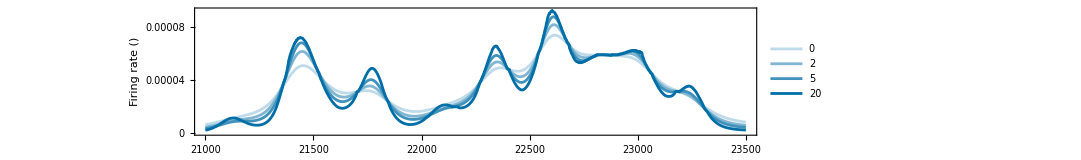

```mathematica
ListLinePlot[datal,AspectRatio->1/5,Frame->True,ImageSize->800,PlotStyle->(Lighter[color,#]&/@{.75,.5,.25,0.}),
PlotLegends->Placed[LineLegend[Text[#,Background->Opacity[.8,White]]&/@{0,2,5,20},Spacings->{.7,.2}],{.05,.7}],
PlotRangePadding->0,ImagePadding->{{90,20},{50,10}},
FrameTicks->{{tickFunc[##]&,None},{tickFunc[##]&,None}},
BaseStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->sbase},
LabelStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->slabel},
FrameStyle->Black,
FrameLabel->(Style[#,Black,.85saxes]&/@{"Chromosome position (kb)",Style[Row[{"Firing rate (",MaTeX["f",FontSize->.85saxes+4],")"}],FontFamily->"Bitstream Vera Sans",.85saxes]})]
```

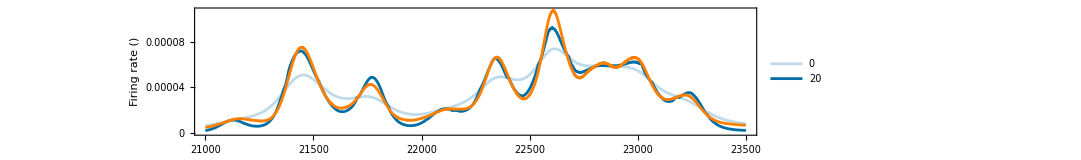

```mathematica
data0=datal[[1]][[All,2]];
fun=Interpolation[data0,InterpolationOrder->3];
g[x_]=D[fun[x],{x,2}];
ListLinePlot[{datal[[1]],datal[[-1]],Transpose[{Range[21000,23500],(fun[#]-(10^3.75g[#]))&/@Range[0,2500]}]},
PlotRange->Automatic,Frame->True,AspectRatio->1/5,Frame->True,ImageSize->800,PlotStyle->{Lighter[color,0.75],color,Orange},
PlotLegends->Placed[LineLegend[Text[#,Background->Opacity[.8,White]]&/@{0,20,MaTeX["f_i^A",FontSize->14]},Spacings->{.7,.2}],{.05,.75}],
PlotRangePadding->0,ImagePadding->{{90,20},{50,10}},
FrameTicks->{{tickFunc[##]&,None},{tickFunc[##]&,None}},
BaseStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->sbase},
LabelStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->slabel},
FrameStyle->Black,
FrameLabel->(Style[#,Black,.85saxes]&/@{"Chromosome position (kb)",Style[Row[{"Firing rate (",MaTeX["f",FontSize->.85saxes+4],")"}],FontFamily->"Bitstream Vera Sans",.85saxes]})
]//Quiet
```

```mathematica
time0=Table[RTf[2501,f,1.4],{f,datal[[1]][[All,2]]}];
time2=Table[RTf[2501,f,1.4],{f,datal[[2]][[All,2]]}];
time5=Table[RTf[2501,f,1.4],{f,datal[[3]][[All,2]]}];
time20=Table[RTf[2501,f,1.4],{f,datal[[-1]][[All,2]]}];
```

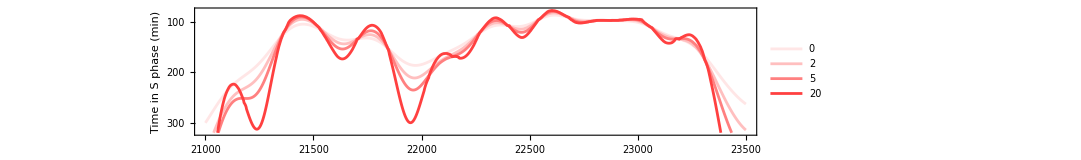

```mathematica
ListLinePlot[Transpose[{Range[21000,23500],#}]&/@{time0,time2,time5,time20},ScalingFunctions->{Identity,"Reverse"},
PlotRange->{320,Automatic},Frame->True,AspectRatio->1/5,Frame->True,ImageSize->800,PlotStyle->(Lighter[Red,#]&/@({.9,.75,.5,0.25})),
PlotLegends->Placed[LineLegend[Text[#,Background->Opacity[0,White]]&/@{0,2,5,20},Spacings->{.7,.2}],{.05,.7}],
PlotRangePadding->0,ImagePadding->{{90,20},{50,10}},
FrameTicks->{{tickFunc[##]&,None},{tickFunc[##]&,None}},
LabelStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->slabel},
FrameStyle->Black,
BaseStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->sbase},FrameLabel->({Style["Chromosome position (kb)",Black,.85saxes],Style["Time in S phase (min)",Black,.78saxes]})
]//Quiet
```

```mathematica
time0=Table[RTf[2501,f,1.4],{f,datal[[1]][[All,2]]}];
time20=Table[RTf[2501,f,1.4],{f,datal[[-1]][[All,2]]}];
timehill=Table[RTf[2501,f,1.4],{f,(fun[#]*(1-10^3.8g[#]/fun[#]))&/@Range[0,2500]}]//Quiet;
```

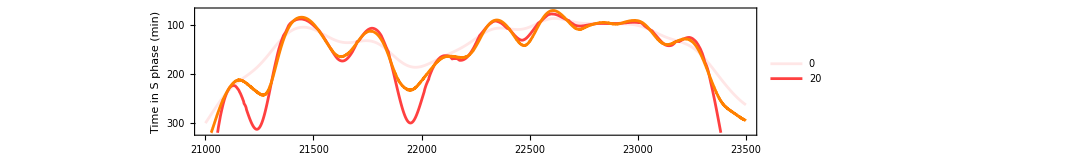

```mathematica
ListLinePlot[Transpose[{Range[21000,23500],#}]&/@{time0,time20,timehill},ScalingFunctions->{Identity,"Reverse"},
PlotRange->{320,Automatic},Frame->True,AspectRatio->1/5,Frame->True,ImageSize->800,PlotStyle->{Lighter[Red,0.9],Lighter[Red,0.25],Orange},
PlotLegends->Placed[LineLegend[Text[#,Background->Opacity[0,White]]&/@{0,20,MaTeX["T_i^A",FontSize->14]},Spacings->{.7,.2}],{.05,.73}],
PlotRangePadding->0,ImagePadding->{{90,20},{50,10}},
FrameTicks->{{tickFunc[##]&,None},{tickFunc[##]&,None}},
LabelStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->slabel},
FrameStyle->Black,
BaseStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->sbase},FrameLabel->({Style["Chromosome position (kb)",Black,.85saxes],Style["Time in S phase (min)",Black,.78saxes]})
]//Quiet
```

## Figure error

```mathematica
List[1,2,3]
```

{1,2,3}

```mathematica
errl={};
Do[
err=ToExpression[Import["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Whole-Genome\\HeLa-S3\\fit_[HeLa-S3]chr["<>ToString@j<>"]_Whole-Genome\\fitfunction_error.txt","Lines"]][[1;;21]];
AppendTo[errl,Transpose[{Range[0,20],err}]],
{j,Range[22]}];
```

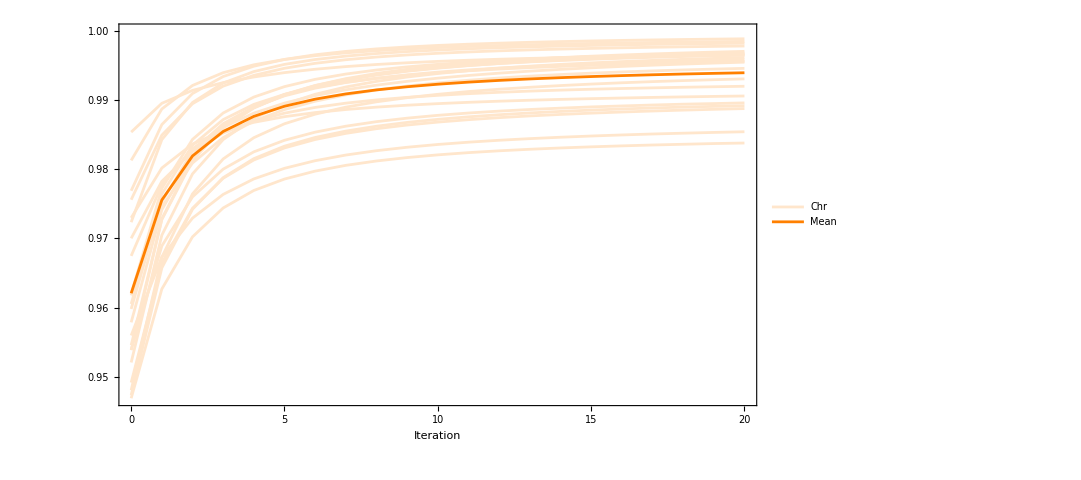

```mathematica
ListLinePlot[Append[errl,Mean[errl]],
Frame->True,AspectRatio->3/5,Frame->True,ImageSize->800,PlotStyle->Append[ConstantArray[Lighter[Orange,0.8],22],Orange],
PlotLegends->Placed[Join[ConstantArray[None,21],{Style["Chr",FontFamily->"Bitstream Vera Sans",sbase]},{Style["Mean",FontFamily->"Bitstream Vera Sans",sbase]}],{0.94,0.09}],
PlotRangePadding->0,PlotRange->{{0,20},{Automatic,1}},ImagePadding->{{90,20},{50,10}},
FrameTicks->{{tickFunc[##]&,None},{tickFunc[##]&,None}},
LabelStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->slabel},
FrameStyle->Black,
BaseStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->sbase},FrameLabel->(Style[#,Black,.85saxes]&/@{"Iteration",Rotate[MaTeX["R^2",FontSize->saxes],-Pi/2]})]
```

## high-res

```mathematica
values={10,20,30,40,50}//N;

(*Calculate the sum of the indices for the non-zero values*)
indexSum=Total[PositionIndex[Select[values,#!=0&]]];

(*Count the non-zero values*)
countNonZero=Count[values,x_/;x!=0];

(*Compute the average index for the non-zero values*)
averageIndex=If[countNonZero!=0,indexSum/countNonZero,None];

Print["Average index: ",averageIndex];
```

Average index: {3}

```mathematica
Mean[values]
```

30.

```mathematica
{2,1,10}//Mean//N
```

4.33333

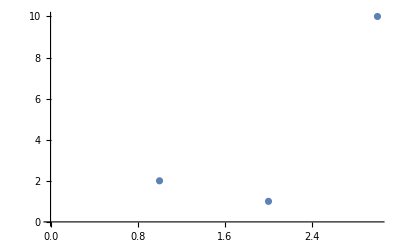

```mathematica
ListPlot[{2,1,10}]
```

```mathematica
data={4,4,4,4,5,5,6,6,6,3,3,4,3,3,3,3,2,2,2,2,1,1,1,1,1,1,1,0,0,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,12,0,12,12,11,6,7,7,7,7,6,5,5,5,5,4,4,4,3,3,3,3,3,3,3,3,3,3,3,4,4,5,6,8,9,9,11,11,11,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,12,12,12,12,11,11,11,9,8,8,6,5,4,4,3,3,3,2,2,2,2,2,2,2,1,1,1,2,2,2,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,2,2,1,0,0,1,2,2,2,3,3,3,3,3,3,3,3,3,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,3,3,3,3,3,3,4,4,3,3,3,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,2,2,2,3,3,3,4,4,5,7,7,11,11,11,11,11,11,11,11,11,11,11,11,11,9,9,11,11,11,11,12,12,12,12,12,12,12,12,12,12,11,11,11,9,9,8,7,6,5,4,4,4,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,0,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,2,2,2,2,3,3,3,4,4,5,6,7,8,8,8,8,8,8,8,8,8,8,7,6,6,5,5,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,5,6,6,6,6,5,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,3,3,3,3,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,2,2,2,2,2,2,2,1,1,1,2,2,2,2,2,2,2,2,3,3,3,3,3,2,2,2,2,2,2,2,2,1,1,1,2,2,2,3,3,3,3,3,3,3,3,3,3,4,4,5,6,7,7,8,8,8,9,9,9,9,9,9,9,8,8,8,8,11,11,6,6,5,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,2,2,2,2,2,2,3,3,3,2,3,3,3,3,3,3,3,4,4,5,7,8,9,9,11,11,11,11,11,11,11,11,9,9,8,7,6,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,3,3,3,4,4,5,6,8,8,8,8,8,8,6,5,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,5,6,7,8,8,8,7,6,6,5,4,4,3,3,3,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,2,2,1,1,0,1,2,2,2,3,3,3,3,3,3,3,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,3,3,3,3,4,4,4,6,6,6,6,5,4,4,3,3,3,3,3,4,4,4,5,6,6,6,7,8,8,8,9,9,9,9,11,11,11,11,11,11,11,11,12,12,12,13,14,14,14,14,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,13,13,12,12,11,11,9,9,8,7,6,6,7,8,8,8,8,8,7,6,6,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,3,3,3,3,3,3,3,3,3,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,5,6,6,7,8,8,9,9,9,11,11,11,11,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,12,12,12,13,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,13,12,12,12,11,11,10,9,9,8,7,6,5,5,5,5,6,6,6,6,7,8,8,8,8,8,8,8,9,9,9,9,9,9,8,8,7,8,8,8,9,9,9,11,11,11,11,12,12,12,12,12,11,11,11,9,9,8,7,6,5,4,4,5,6,6,7,7,7,6,5,4,4,4,3,3,3,4,4,4,4,6,6,6,6,6,6,5,5,4,4,4,4,4,3,3,4,4,4,4,5,6,7,7,7,6,5,5,5,5,6,6,4,4,4,4,4,4,5,6,6,7,6,5,5,5,6,6,6,6,6,6,6,5,4,4,4,4,4,4,3,3,3,4,4,4,4,4,4,4,4,4,7,6,6,7,7,7,7,6,4,4,3,3,3,2,2,2,2,3,3,3,4,4,5,5,5,4,4,5,6,6,6,6,6,6,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,4,4,4,5,7,8,8,9,9,10,11,11,11,12,12,12,12,12,12,12,13,13,13,13,12,12,11,11,11,9,9,9,9,8,7,7,4,4,4,4,4,4,5,7,8,8,9,9,11,11,11,11,11,12,12,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,15,15,15,14,14,14,14,13,13,13,12,12,12,12,12,12,12,12,12,11,11,10,9,9,9,8,8,7,6,4,4,3,3,3,4,4,4,4,6,8,8,9,9,9,11,11,11,11,11,11,11,11,11,9,9,9,9,9,9,8,8,8,7,7,6,5,4,4,4,4,3,3,3,3,3,3,3,3,3,4,4,5,7,8,8,9,9,9,9,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,13,13,13,13,13,13,13,13,13,13,13,13,13,12,12,12,13,13,14,14,14,14,14,14,15,14,15,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,13,14,14,14,14,14,14,13,12,11,11,9,9,9,8,7,6,4,4,3,3,3,3,3,2,2,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,3,3,3,3,3,4,4,4,4,4,4,4,6,6,7,7,8,8,8,8,8,9,8,8,8,8,8,8,7,7,6,5,4,4,4,4,4,5,7,7,8,8,8,8,9,9,9,9,9,10,11,11,11,11,10,11,11,11,11,11,11,9,9,9,9,9,8,8,6,5,4,4,4,4,4,4,4,4,4,7,8,8,8,8,8,8,7,7,6,6,6,5,4,4,4,4,4,4,4,6,7,8,9,9,9,10,11,11,11,10,9,9,9,9,8,9,9,8,8,8,8,8,8,8,8,8,7,6,6,6,5,6,6,6,6,5,5,5,4,4,5,4,4,4,4,4,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,5,6,7,8,9,9,10,11,11,11,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,10,9,9,9,9,9,9,9,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,9,9,9,9,9,9,10,10,9,9,9,9,9,9,9,9,10,10,11,11,11,11,11,11,11,11,11,11,11,10,9,9,9,8,8,7,6,5,4,4,4,4,4,4,4,4,3,3,3,3,4,4,5,6,7,8,8,8,8,8,9,9,9,9,8,8,8,8,8,9,9,9,11,11,12,12,12,12,13,13,13,13,13,13,13,13,13,13,14,14,13,13,13,13,13,13,13,13,12,12,13,13,13,13,13,13,13,13,12,12,12,12,12,12,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,14,14,15,15,15,15,15,14,14,14,15,15,15,15,15,15,15,15,14,14,15,14,14,14,14,15,15,15,15,15,15,15,15,15,15,14,14,15,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,12,12,12,11,11,10,9,9,9,8,9,8,7,6,5,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,3,3,3,3,3,3,3,3,3,4,4,4,5,6,7,8,8,8,8,8,8,8,8,7,7,7,6,6,5,4,4,4,4,4,4,4,4,6,7,8,8,8,8,7,6,5,4,4,3,3,3,3,4,4,4,4,3,3,3,3,3,3,3,4,4,4,5,5,6,6,7,7,7,5,4,4,4,4,4,4,4,5,6,6,6,5,5,4,4,4,4,4,4,4,4,4,5,6,7,7,7,8,8,8,8,9,9,9,9,8,8,8,7,7,7,7,7,7,7,7,7,6,6,6,6,6,5,4,4,4,4,4,4,4,5,5,5,5,5,5,6,6,6,6,6,6,6,6,7,7,7,7,7,7,8,8,8,8,9,9,9,10,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,9,9,9,9,9,8,8,7,6,6,6,6,6,6,7,7,6,6,5,6,6,5,4,4,4,5,5,6,4,4,4,4,4,5,4,5,5,6,7,8,8,9,9,9,9,9,11,11,9,9,9,9,9,9,9,9,9,9,9,9,9,9,14,9,9,9,10,10,0,0,0,0,0,0,0,0,0,0,1,1,2,0,0,0,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,13,13,14,14,12,12,12,12,12,12,12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,15,15,15,15,11,10,9,12,12,11,11,9,8,8,8,9,9,9,9,12,12,12,4,9,9,9,11,11,11,11,6,7,7,7,6,7,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,6,6,8,8,9,9,9,9,9,8,8,8,8,8,7,7,7,7,7,7,7,6,6,5,5,6,6,6,6,6,6,6,5,4,4,4,4,4,4,4,3,4,4,4,4,4,4,4,4,4,5,5,5,4,4,4,4,4,4,4,4,5,6,6,5,4,5,6,6,6,4,4,4,3,3,3,3,3,3,2,2,2,2,2,2,2,2,3,3,3,2,2,2,1,1,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,4,4,5,7,8,8,8,8,9,9,10,11,11,11,11,9,9,9,8,8,7,5,4,4,3,3,3,2,2,1,1,2,12,12,12,2,2,2,2,2,2,2,3,3,3,3,4,4,3,3,3,3,3,3,3,3,2,2,1,1,1,1,12,12,2,2,2,2,2,2,2,2,2,2,2,2,1,0,0,0,1,1,2,2,1,2,2,2,2,1,1,1,1,1,2,2,2,2,3,3,3,4,4,5,6,7,8,9,9,9,10,11,10,9,9,8,8,6,6,6,7,8,9,9,9,11,12,12,12,12,13,13,13,13,13,14,13,13,12,12,12,12,12,12,12,12,11,11,9,9,8,8,6,5,4,4,4,4,4,3,3,3,3,3,3,3,4,4,5,6,6,6,5,5,4,4,3,3,3,2,2,2,2,2,3,3,3,5,6,6,6,5,5,5,4,4,4,3,3,3,4,4,4,4,4,4,4,4,3,3,3,4,4,4,4,5,6,7,7,7,8,8,9,9,9,9,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,9,9,9,9,11,11,11,11,11,11,11,11,11,11,11,9,9,9,8,8,7,5,4,4,4,4,4,4,4,4,6,6,8,8,9,9,11,11,11,11,11,11,11,11,11,9,9,9,8,8,8,7,7,6,6,6,6,6,5,5,4,4,4,4,4,4,4,4,3,4,4,4,4,3,3,3,3,3,3,4,4,4,5,6,7,8,8,8,8,8,8,8,7,8,8,8,8,8,7,6,6,6,7,7,7,7,7,7,7,8,8,9,9,9,9,9,11,11,11,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,7,6,5,5,5,4,4,4,4,4,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,6,6,6,6,6,6,5,5,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,4,4,4,5,6,7,8,8,9,9,9,11,11,11,11,11,9,9,8,8,7,7,8,8,9,9,9,11,11,11,11,11,11,11,11,11,11,11,11,11,9,9,9,9,11,11,11,12,12,13,14,14,14,14,14,14,14,14,15,15,14,14,14,14,13,13,12,12,12,12,11,11,9,9,8,7,6,5,4,4,4,5,6,6,5,5,4,4,4,4,4,4,4,4,5,4,4,4,4,4,4,4,4,4,4,4,4,5,6,6,5,5,4,4,4,4,3,3,3,3,3,3,3,3,4,4,4,4,4,5,5,6,6,6,4,4,4,4,3,3,3,4,4,4,6,7,8,9,9,11,11,11,11,11,11,11,11,9,9,9,9,9,9,8,8,8,8,8,8,8,7,6,6,5,4,4,4,4,4,4,4,4,4,4,4,5,5,5,4,4,4,4,5,6,6,6,6,7,7,8,8,8,8,8,8,8,9,9,9,9,8,8,8,8,8,8,7,6,6,7,8,8,9,9,8,8,8,9,9,9,9,9,9,9,9,9,11,11,9,9,9,9,8,8,8,8,8,9,9,9,9,9,9,9,9,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,11,11,11,11,11,11,9,9,9,8,8,7,6,4,4,4,3,3,3,3,4,4,4,4,4,4,4,6,7,8,8,9,9,9,9,9,10,11,11,11,11,11,11,11,11,9,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,11,11,11,10,10,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,9,9,9,9,9,9,9,9,11,11,12,12,11,0,11,11,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,7,7,7,7,6,6,6,6,5,4,4,4,4,3,3,3,3,3,3,3,3,4,4,4,4,3,3,3,3,3,3,2,3,3,3,3,3,3,3,2,2,2,1,1,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,5,6,6,6,6,6,6,6,6,6,6,5,5,5,5,6,6,7,8,8,9,9,10,11,11,12,12,12,13,13,14,14,14,14,14,14,14,14,14,13,13,12,12,11,11,10,9,9,8,8,7,6,6,6,6,6,8,8,9,9,9,9,9,9,9,9,9,11,11,11,11,11,11,11,11,11,11,11,9,9,8,7,6,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,6,6,7,8,8,9,9,9,11,11,11,11,11,11,11,11,11,10,9,9,8,8,6,6,6,6,5,4,4,4,4,4,6,7,8,9,9,9,10,11,11,11,11,11,11,11,11,9,9,9,9,9,11,11,12,12,13,13,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,13,13,13,12,12,12,11,11,11,12,12,13,13,12,12,12,11,11,12,11,11,11,10,9,9,9,9,9,8,9,9,9,9,9,9,9,10,10,10,9,9,9,9,10,11,11,11,10,10,9,9,9,9,8,8,6,5,4,4,4,3,4,4,5,6,7,8,8,8,8,8,7,6,6,6,7,8,9,9,9,11,11,11,11,11,11,11,11,11,11,11,12,12,12,11,11,11,11,11,11,11,11,11,10,9,9,8,7,6,5,5,5,6,6,6,7,8,8,8,7,7,7,7,7,8,8,8,6,4,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,5,6,7,8,8,8,8,8,8,8,7,6,5,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,4,4,4,4,4,5,5,6,5,5,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,5,6,6,6,7,7,7,6,5,5,4,4,4,4,4,3,3,4,4,5,6,6,7,8,8,8,8,8,9,9,8,8,9,9,9,8,8,7,6,5,5,4,4,4,5,5,4,4,4,4,3,3,3,3,3,3,3,3,4,4,4,5,6,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,8,8,8,8,7,6,5,4,5,5,6,6,6,7,7,6,7,7,7,7,8,8,8,8,11,4,4,4,4,4,4,4,5,5,6,6,6,6,5,5,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,5,5,6,7,7,7,7,7,6,6,7,8,9,9,9,10,11,11,12,12,12,13,13,14,14,14,14,14,14,14,14,14,14,15,15,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,14,14,14,14,14,14,14,14,14,14,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,13,12,12,12,11,11,9,9,9,9,9,8,8,7,6,6,6,6,8,8,9,10,10,11,12,12,12,13,13,13,13,13,13,12,12,12,12,12,0,0,12,12,12,0,0,0,0,0,0,0,0,0,12,12,11,11,11,11,9,9,8,8,6,6,6,6,6,6,5,4,4,4,4,4,4,4,4,4,4,4,5,6,7,11,11,0,0,0,0,11,11,11,11,11,11,11,12,12,12,11,11,9,9,9,8,7,5,5,5,5,5,5,5,5,6,7,8,8,8,8,8,8,8,9,9,9,9,11,11,12,12,12,12,13,13,13,13,13,13,13,13,13,13,12,12,12,11,11,9,9,8,8,6,5,5,5,8};
```

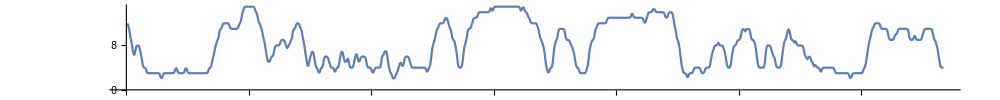

```mathematica
ListLinePlot[GaussianFilter[data[[1000;;2000]],2],AspectRatio->1/10,ImageSize->1000]
```

## IOD plots

```mathematica
cell="HeLa-S3";
chr=1;
cint=Table[{i*10000,(i+1)*10000},{i,Range[0,23]}];
iodlnl={};
Do[
If[FileExistsQ[FileNameJoin[{"C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Large_fit\\"<>cell<>"\\fit_["<>cell<>"]chr["<>ToString@chr<>"]_"<>ToString[j[[1]]]<>"-"<>ToString[j[[2]]],"iods.txt"}]],
iodl=Import["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Large_fit\\"<>cell<>"\\fit_["<>cell<>"]chr["<>ToString@chr<>"]_"<>ToString[j[[1]]]<>"-"<>ToString[j[[2]]]<>"\\iods.txt","Lines"];
iodln=N[ToExpression[StringReplace[#,{"["->"{","]"->"}"}]]]&/@iodl;
AppendTo[iodlnl,iodln]],
{j,cint}];
(*iodlnl2=Flatten[#]&/@Transpose[iodlnl];*)
```

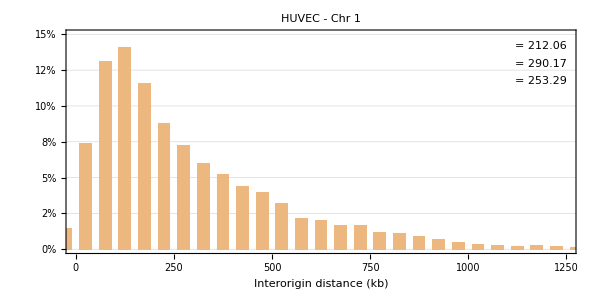

```mathematica
datap=Select[Flatten[iodln],#>20&];

ds=60;cell="HUVEC";
datap=.9#+RandomReal[{-ds,ds}]&/@datap;

f2[d_][{{xmin_,xmax_},{ymin_,ymax_}},___]:=Rectangle[{xmin+d (xmax-xmin)/2,ymin},{xmax-d (xmax-xmin)/2,ymax}]
mean=Mean[datap];
median=Median[datap];
std=StandardDeviation[datap];

tickFunc2=Module[{rawTicks},rawTicks=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.01,.005}][##];
rawTicks=MapAt[Reverse,rawTicks,{All,3}];
MapAt[PercentForm[#/. NumberForm[a_,___]:>PercentForm[Round[a,.01]]]&,rawTicks,{All,2}]]&;


Histogram[datap,{50},"Probability",GridLines->{None,Automatic},Frame->True,
GridLinesStyle->Directive[Lighter[Gray,0.5],Dotted],
ChartStyle->Lighter[RGBColor[0.9,0.6,0.29],0.3],ChartBaseStyle->EdgeForm[{None,Thickness[0],Opacity[1]}],
ChartElementFunction->f2[0.4],
PlotRangePadding->0,
(*FrameTicks->{{tickFunc2[##]&,None},{tickFunc[##]&,None}},*)
FrameTicks->{{tickFunc2[##]&,None},{tickFunc[##]&,None}},

PlotRange->{{0,1250},{0,.15}},
PlotRangeClipping->True,
Epilog->{
Text[MaTeX["\\mu_{\\frac12}",FontSize->sbase+4],Scaled[{dl-0.01,dl2+0.15}],Left,Background->White],
Text["= "<>ToString@Round[N@median,.01],Scaled[{dl+0.03,dl2+0.15}],Left,Background->White],
Text[MaTeX["\\mu",FontSize->sbase+4],Scaled[{dl,dl2+0.07}],Left,Background->None],
Text["= "<>ToString@Round[N@mean,.01],Scaled[{dl+0.03,dl2+0.07}],Left,Background->None],
Text[MaTeX["\\sigma",FontSize->sbase+4],Scaled[{dl,dl2-0.01}],Left,Background->None],
Text["= "<>ToString@Round[N@std,.01],Scaled[{dl+0.03,dl2-0.01}],Left,Background->White]},
FrameStyle->Black,
PlotLabel->cela[cell]<>" - Chr "<>ToString[chr],
BaseStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->sbase},
LabelStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->slabel},
FrameLabel->(Style[#,Black,saxes]&/@{Row[{"Interorigin distance (kb)"}]}),LabelStyle->{10,GrayLevel[0]} ,AspectRatio->1/2,ImageSize->ims]
```

## sigmoid

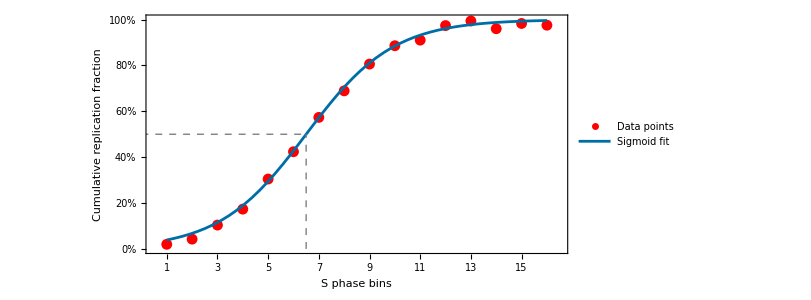

```mathematica
(*Generate 16 points along a sigmoidal curve*)xValues=Range[1,16];
kValue=2.33;  (*This is the true value of k for generating points*)
yValues=100./(1+Exp[-kValue*(xValues-6.5)/4]);

(*Add the points to a list*)
data=Transpose[{xValues,yValues}];

(*Define the sigmoidal function for fitting*)
sigmoidal[x_,k_]:=100/(1+Exp[-k (x-6.5)/4]);

(*Fit the sigmoidal function to the data*)
fit=NonlinearModelFit[data,sigmoidal[x,k],{k},x];

(*Extract the fitted value of k*)
fittedK=fit["BestFitParameters"][[1,2]];

(*Plot the points and the fitted curve*)
Show[ListPlot[{#[[1]],(#[[2]]+RandomReal[{-3,3}])/100}&/@data,PlotStyle->{Red,PointSize[0.013]},PlotLegends->Placed[{"Data points"},{.87,.1}],ImageSize->ims,PlotRange->{{0.5,16.5},{0,1}}],Plot[fit[x]/100,{x,1,16},PlotStyle->color,PlotLegends->Placed[{"Sigmoid fit"},{.87,.18}]],Frame->True,FrameLabel->{"S phase bins","Cumulative replication fraction"},

tickFunc2=Module[{rawTicks},rawTicks=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.01,.005}][##];
rawTicks=MapAt[Reverse,rawTicks,{All,3}];
MapAt[PercentForm[#/. NumberForm[a_,___]:>PercentForm[Round[a,.01]]]&,rawTicks,{All,2}]]&;
tickFunc3=MapAt[Reverse,{All,3}]@*Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.01,.005}];

PlotRangePadding->0,AspectRatio->1/2,
FrameTicks->{{tickFunc2[##]&,None},{Join[{#,#,{0,.01}}&/@Range[16],{{6.5,MaTeX["t_{\\text{rep}}",FontSize->15],{0,0.01}}}],None}},
BaseStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->sbase},
LabelStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->slabel},
Epilog->{Dashed,Gray,Line[{{6.5,0},{6.5,.5}}],Line[{{0,.5},{6.5,.5}}]}
]
```

## Animations

```mathematica
datal={};
Do[
data=ToExpression[Import["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Convergence\\fit_[BJ1]chr[2]_Whole-Genome\\fitfunction_"<>ToString@j<>".txt","Lines"][[21000;;23500]]];
AppendTo[datal,Transpose[{Range[21000,23500],data}]],
{j,0,20}];
```

```mathematica
flist=Table[ListLinePlot[datal[[1;;k]],AspectRatio->1/5,Frame->True,ImageSize->800,PlotStyle->(Lighter[color,#]&/@Range[.75,0,-.036]),PlotLegends->Placed[LineLegend[{Lighter[color,.75-.036 (k-1)]},Text[#,Background->Opacity[.8,White]]&/@{ToString[k-1]},Spacings->{.7,.2}],{.05,.85}],PlotRange->{0,0.000095},PlotRangePadding->0,ImagePadding->{{90,20},{50,10}},FrameTicks->{{tickFunc[##]&,None},{tickFunc[##]&,None}},BaseStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->sbase},LabelStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->slabel},FrameStyle->Black,FrameLabel->(Style[#,Black,.85 saxes]&/@{"Chromosome position (kb)",Style[Row[{"Firing rate (",MaTeX["f",FontSize->.85 saxes+4],")"}],FontFamily->"Bitstream Vera Sans",.85 saxes]})],{k,21}];
```

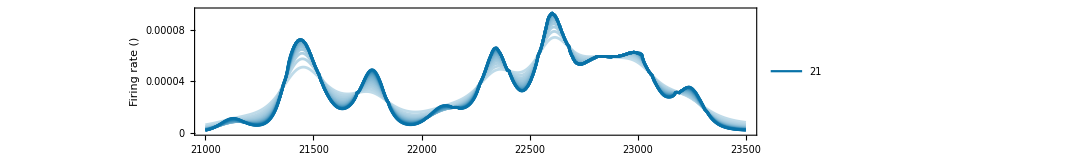

```mathematica
flist[[21]]
```

```mathematica
Export["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Videos\\flisti.mp4",flist,ImageResolution->1080,Antialiasing->True,FrameRate->1]
```

C:\Users\Francisco Berkemeier\Dropbox\Main Work\PostDoc\My Papers\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\Videos\flisti.mp4

```mathematica
timel=Table[RTf[2501,f,1.4],{f,#[[All,2]]}]&/@datal;
```

```mathematica
timlist=Table[ListLinePlot[Transpose[{Range[21000,23500],#}]&/@timel[[1;;k]],ScalingFunctions->{Identity,"Reverse"},
PlotRange->{320,75},Frame->True,AspectRatio->1/5,Frame->True,ImageSize->800,PlotStyle->(Lighter[Red,#]&/@Range[.9,0.25,-.031]),
PlotLegends->Placed[LineLegend[{Lighter[Red,.75-.036 (k-1)]},Text[#,Background->Opacity[.8,White]]&/@{ToString[k-1]},Spacings->{.7,.2}],{.05,.85}],PlotRange->{0,0.00009},PlotRangePadding->0,ImagePadding->{{90,20},{50,10}},FrameTicks->{{tickFunc[##]&,None},{tickFunc[##]&,None}},BaseStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->sbase},LabelStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->slabel},FrameStyle->Black,FrameLabel->(Style[#,Black,.85 saxes]&/@{"Chromosome position (kb)",Style["Time in S phase (min)",Black,.78saxes]})
]//Quiet,{k,21}];
```

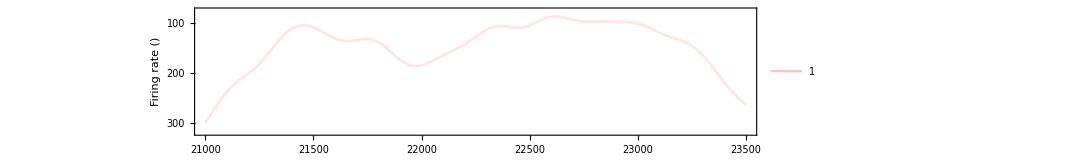

```mathematica
timlist[[1]]
```

```mathematica
Export["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Videos\\timlist.mp4",timlist,ImageResolution->1080,Antialiasing->True,FrameRate->1]
```

C:\Users\Francisco Berkemeier\Dropbox\Main Work\PostDoc\My Papers\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\Videos\timlist.mp4

```mathematica
fitiml=Table[Column[{flist[[j]],timlist[[j]]}],{j,21}];
Export["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Videos\\fitiml.mp4",fitiml,ImageResolution->1080,Antialiasing->True,FrameRate->1]
```

C:\Users\Francisco Berkemeier\Dropbox\Main Work\PostDoc\My Papers\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\Videos\fitiml.mp4

## Inverting tests

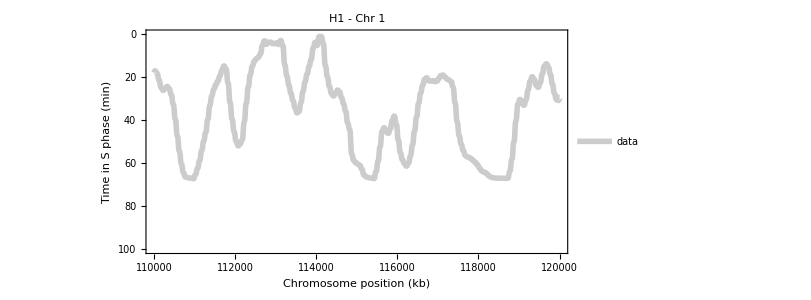

```mathematica
cell="H1";
chr=1;
minp=110000;
maxp=120000;
ext="_classic";
st[s_]:=Style[s,FontFamily->"Bitstream Vera Sans",Black,14]
timereal=Import["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Large_fit\\"<>cell<>"\\fit_["<>cell<>"]chr["<>ToString@chr<>"]_"<>ToString@minp<>"-"<>ToString@maxp<>ext<>"\\time_real.txt","Lines"];
timereal=Flatten[ToExpression[StringSplit[#,","]]&/@timereal];
timesim=Import["C:\\Users\\"<>user<>"\\Dropbox\\Main Work\\PostDoc\\My Papers\\A Whole-Genome Mathematical Model of Chemotherapy's Influence on DNA Replication\\Data\\Large_fit\\"<>cell<>"\\fit_["<>cell<>"]chr["<>ToString@chr<>"]_"<>ToString@minp<>"-"<>ToString@maxp<>ext<>"\\time_sim.txt","Lines"];
timesim=Flatten[ToExpression[StringSplit[#,","]]&/@timesim];
AppendTo[timereal,timereal[[-1]]];
AppendTo[timesim,timesim[[-1]]];

ListLinePlot[{Transpose[{Range[minp,maxp],timereal}]},
Frame->True,ImageSize->ims,PlotRange->{0,100},
AspectRatio->1/2,
PlotStyle->{{Opacity[.4,Gray],AbsoluteThickness[4]},{Opacity[.55,Red],AbsoluteThickness[4]}},
PlotLegends->Placed[LineLegend[{st@" data",st@" bcs"},Spacings->{0,-0.8},LegendMarkerSize->30],{.91,.89}],
PlotRangePadding->0,ImagePadding->{{60,30},{All,All}},
FrameTicks->{{tickFunc[##]&,None},{tickFunc[##]&,None}},ScalingFunctions->{Automatic,"Reverse"},
BaseStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->sbase},
LabelStyle->{FontFamily->"Bitstream Vera Sans",Black,FontSize->slabel},
PlotLabel->cela[cell]<>" - Chr "<>ToString[chr],
FrameStyle->Black,
FrameLabel->(Style[#,Black,saxes]&/@{"Chromosome position (kb)",Style[Row[{"Time in S phase (min)"}],FontFamily->"Bitstream Vera Sans",16]})

(*,Epilog->{
Text[MaTeX["v=0.28\\text{ kb/min}",FontSize->sbase+4],Scaled[{0.5,0.1}],Center,Background->White]}*)
]
```

```mathematica
(* Fraction of replicated DNA *)
rlen[t_,trep_,r_]:=1/(1+(trep/t)^r)
slen[t_,trep_,r_]:=1-rlen[t,trep,r]
```

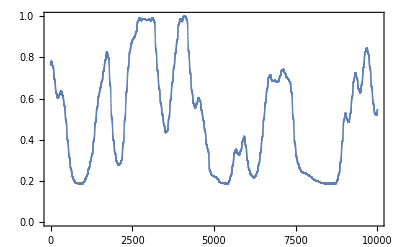

```mathematica
trep=Median[timereal];
slength=slen[#,trep,2]&/@timereal;
ListPlot[slength,Frame->True]
```

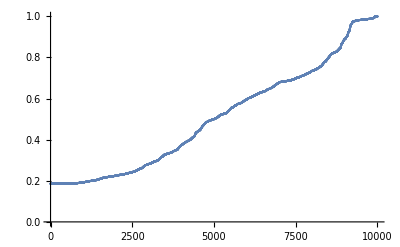

```mathematica
ListPlot[Sort[slength]]
```

```mathematica
ET[j_,x_List,n_,L_]:=Sum[(Exp[-Sum[(k-Abs[i]) x[[Mod[j+i,n,1]]],{i,-k,k}]]-Exp[-Sum[(k+1-Abs[i]) x[[Mod[j+i,n,1]]],{i,-k,k}]])/Sum[x[[Mod[j+i,n,1]]],{i,-k,k}],{k,0,L}]
```

```mathematica
ET[1,timereal,Length[timereal],1000]
```

0.0560564208767014653371

```mathematica
Clear[v,f]
```

```mathematica
-(1/(2v))D[Log[E^(-f v t^2)],{t,2}]//FullSimplify
```

f

```mathematica
slen
```

```mathematica
-(1/(2v))D[Log[E^(-f v t^2)],{t,2}]//FullSimplify
```